## Setup

#### Docked cell

```mathematica
CurrentValue[EvaluationNotebook[],DockedCells]={};
```

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/nikm/DeveloperDockedCell"]["ProcessTheoryLoader`",FileNameJoin[{NotebookDirectory[],"..","ProcessTheory"}],{"ProcessTheory`Port`","ProcessTheory`Diagram`","ProcessTheory`Diagram`ToDiagram`"}]
```

#### Usage

```mathematica
symbolPages=FirstCase[First[PacletFind["ProcessTheory"]]["Extensions"],{"Kernel",___,"Symbols"->symbols_,___}:>Map[ExpandFileName@FileNameJoin[{NotebookDirectory[], "..", "..", "Mathematica", "Documentation", "English", "System", "ReferencePages", "Symbols",#}]&,StringReplace[symbols,RegularExpression["System`(.+)"]:>"$1.nb"]]];
```

```mathematica
usage = Map[file |->
	Block[{nb = NotebookOpen[file, Visible -> False], usage},
		NotebookFind[nb, "Usage", Next, CellStyle];
		usage = FileBaseName[file] <> "::usage = " <> ExportString[ToString[RawBoxes[NotebookRead[nb]], StandardForm], "WL", "Comments" -> None];
		NotebookClose[nb];
		usage
	],
	symbolPages
];
```

```mathematica
With[{file = File[ExpandFileName @ FileNameJoin[{NotebookDirectory[], "..", "ProcessTheory", "Kernel", "Usage.m"}]]},
	BinaryWrite[
		file,
		StringRiffle[{"Package[\"ProcessTheory`\"]", Splice[usage]}, "\r\n\r\n\r\n"]
	];
	Close[file];
]
```

```mathematica
Scan[If[!CurrentValue[#,Visible],NotebookClose[#]]&,Notebooks[]]
```

```mathematica
?ProcessDiagram
```

```mathematica
?DiagramPlot
```

#### SaveReadable

```mathematica
ResourceFunction["SaveReadableNotebook"][EvaluationNotebook[],NotebookFileName[]];
```

#### Upload

```mathematica
URLShorten["https://wolfr.am/1q5XjM6t9","ProcessTheory.paclet"]
```

https://wolfr.am/1q5XjM6t9

```mathematica
PacletInstall["https://www.wolframcloud.com/obj/nikm/ProcessTheoryLoader.paclet",ForceVersionInstall->True]
```

## Design

Port

Double dagger monoidal structure with PortDual, (Port[“0”], PortSum), (Port[“1”], PortProduct): a⊗(b^*⊕c⊕0)⊗(1⊗d)

Diagram

A tree with double monoidal structure: (Node[“0”], NodeSum)  and (Node[“1”], NodeProduct)

Output and Input ports

DiagramGraph - up-to two identical ports, either wire or a free port
DiagramHypergraph - arbitrary wire arity (spiders)

DiagramNetwork

Unordered list of nodes

DiagramGrid

Aligned grid of nodes

## Playground

#### HVM

```mathematica
PacletDirectoryLoad["~/src/wolfram/WL-FunctionalParsers-paclet"];
<<AntonAntonov`FunctionalParsers`

numOperators=<|"+"->"ADD","-"->"SUB",":-"->"FSUB","*"->"MUL","/"->"DIV",":/"->"FDIV","%"->"REM",":%"->"FREM","="->"EQ","!"->"NEQ","<<"->"SHL",":<<"->"FSHL",">>"->"SHR",":>>"->"FSHR","<"->"LT",">"->"GT","&"->"AND","|"->"OR","^"->"XOR"|>;

pALPHANUMERIC=ParsePredicate[StringMatchQ[RegularExpression["[a-zA-Z][a-zA-Z0-9_.-/]*"]]];
pNUMERIC=ParsePredicate[StringMatchQ[NumberString]];

pCON=ParseParenthesized[pTREE⊗pTREE];
pDUP=ParseCurlyBracketed[pTREE⊗pTREE];
pNUMOP=ParseBracketed[Apply["NUMOP"]⊙(ParseChoice@@KeyValueMap[{token,op}|->(op&)⊙ParseToken[{token}],numOperators]⊗ParseOption[Interpreter["HexInteger"]⊙ParsePredicate[True&]])]⊕pTREE;
pOPE=ParseSymbol["$"]⊳ParseParenthesized[pNUMOP⊗pTREE];
pSWI=ParseSymbol["?"]⊳ParseParenthesized[pTREE⊗pTREE];

pNODE="ERA"⊙ParseSymbol["*"]⊕
"REF"⊙(ParseSymbol["@"]⊳pALPHANUMERIC)⊕
"NUM"⊙pNUMERIC⊕
Apply["CON"]⊙pCON⊕
Apply["DUP"]⊙pDUP⊕
Apply["OPR"]⊙pOPE⊕
Apply["SWI"]⊙pSWI;

ParseRecursiveDefinition[pTREE,pALPHANUMERIC⊕pNODE];

pREDEX=(pTREE⊲ParseSymbol["~"])⊗pNUMOP;
pNET=Apply["NET"]⊙(pTREE⊗ParseShortest[ParseMany[Apply["REDEX"[#1,Sequence@@#2]&]⊙(ParseSymbol["&"]⊳(Replace[{{}->True,_->False}]⊙ParseOption[ParseSymbol["!"]])⊗pREDEX)]]);
pBOOK=ParseShortest[ParseMany[Apply[Rule]⊙((ParseSymbol["@"]⊳pALPHANUMERIC)⊗(ParseSymbol["="]⊳pNET))]];
(*
ClearAll[CircleTimes, CirclePlus, CircleDot]*)
```

```mathematica
ClearPorts[] := Quiet[Remove[Evaluate[Join[Names["Global`@$*"], Select[Names["System`@$*"], StringMatchQ[ToString[FullForm[Symbol[#]]], "\\[Formal" ~~ _ ~~"]"~~___] &]]]]]
```

```mathematica
TokenizeHVM[hvm_]:=ParseToTokens[hvm,Join[Select[Keys@numOperators,StringLength[#]>1&],Characters["$?!+-*@~&=:|<>(){}[]"]]]
```

```mathematica
ParseHVM//ClearAll
ParseHVM[file_?FileExistsQ]:=ParseHVM@Import[file,"String"]
ParseHVM[src_String]:=Block[{parse,result},
<<AntonAntonov`FunctionalParsers`;
parse=First@pBOOK@TokenizeHVM[src];
result=If[parse[[1]]==={},Association@parse[[2]],Failure["ParseHVM",<|"MessageTemplate"->"Failed parsing HVM: ``","MessageParameters"->{parse[[1]]}|>]];
ClearAll[CircleTimes, CirclePlus, CircleDot];
result
]
```

```mathematica
hvm=ParseHVM["/Users/swish/src/Bend/examples/Church.bend.hvmc"];
```

```mathematica
HVMToDiagrams[net_]:=Block[{$ModuleNumber=1,vars=<||>,compileNet, makeNode = Diagram[##, "Shape" -> "Triangle"] &,uniqueX=Function[Interpretation["x",Evaluate@Unique[x]]]},
compileNet=Replace[{
"ERA"[_]->{makeNode["δ", uniqueX[]]},
"REF"[ref_]:>{makeNode["REF"[ref],uniqueX[]]},
"NUM"[n_]:>{makeNode["NUM"[Interpreter["Number"]@n],uniqueX[]]},
"NUMOP"[op_,args_List]:>{makeNode[op[args],uniqueX[]]},
"NET"[root_,bag_]:>Join[compileNet[root],Replace[bag,"REDEX"[par_,x_,y_]:>With[{a=compileNet[x],b=compileNet[y]},Splice@Join[a,If[StringQ[a[[1]]]||StringQ[b[[1]]],b,MapAt[makeNode[#,"OutputPorts"->a[[1]]["OutputPorts"]] &, b, {1}]]]],{1}]],
node_[l_,r_]:>With[{a=compileNet[l],b=compileNet[r]},Join[{makeNode[Replace[node,{"DUP"->"δ","CON"->"γ"}],{If[StringQ[a[[1]]],vars[a[[1]]],a[[1]]["OutputPorts"][[1]]],If[StringQ[b[[1]]],vars[b[[1]]],b[[1]]["OutputPorts"][[1]]]},uniqueX[]]},a,b]],
var_String:>(If[!KeyExistsQ[vars,var],AppendTo[vars,var->Interpretation["v",Evaluate@Unique[Symbol["v"<>var]]]]];{var})
}];

DiagramNetwork[##,"BinarySpiders"->False]&@@DeleteCases[compileNet[net],_String]
]
```

```mathematica
HVMToDiagrams[hvm["S"]]
```

-Graphics-

```mathematica
HVMToDiagrams/@hvm
```

<|S→-Graphics-,Z→-Graphics-,decode→-Graphics-,decode__C0→-Graphics-,encode→-Graphics-,encode__C0→-Graphics-,main→-Graphics-,mul→-Graphics-|>

#### Ports

```mathematica
Port[a]["Properties"]
```

{Arity,Data,Dual,HoldExpression,Label,Name,Neutral,NeutralQ,Properties,Reverse,Type,Types,View}

```mathematica
Port[a]["Type"]
```

T

```mathematica
Port[a,"AnyType"]
```

a

```mathematica
Port[SuperStar[a]]
```

a^*

```mathematica
Port[a⊗b]
```

a⊗b

```mathematica
["Dual"]
```

(a⊗b)^*

```mathematica
["Neutral"]
%["NeutralQ"]
```

a⊗b

True

```mathematica
Port[a⊗(b⊕SuperStar[c])]
```

Port[Association[Expression :> PortProduct[Port[Association[Expression :> a, NeutralQ -> False, Type -> T]], 
     Port[Association[Expression :> PortSum[Port[Association[Expression :> b, NeutralQ -> False, Type -> T]], Port[Association[Expression :> PortDual[c], NeutralQ -> False, 
           Type -> SuperStar[T]]]], NeutralQ -> False, Type -> T ⊕ SuperStar[T]]]], NeutralQ -> False, Type -> T ⊗ (T ⊕ SuperStar[T])]]

```mathematica
Port[a⊗(b⊕SuperStar[c])]["Neutral"]
```

Port[Association[Expression :> PortProduct[Port[Association[Expression :> a, NeutralQ -> True, Type -> T]], 
     Port[Association[Expression :> PortSum[Port[Association[Expression :> b, NeutralQ -> True, Type -> T]], 
         Port[Association[Expression :> PortDual[Port[Association[Expression :> c, NeutralQ -> True, Type -> T]]], NeutralQ -> True, Type -> SuperStar[T]]]], NeutralQ -> True, 
       Type -> T ⊕ SuperStar[T]]]], NeutralQ -> True, Type -> T ⊗ (T ⊕ SuperStar[T])]]

```mathematica
Port[a⊗(b⊕SuperStar[c])]["PortTree"]//ExpressionTree
```

-Graphics-

```mathematica
PortProduct[Port[Association["Expression" :> a, "Type" -> T]], 
  Port[Association["Expression" :> PortSum[Port[Association["Expression" :> b, "Type" -> T]], Port[Association["Expression" :> PortDual[c], "Type" -> SuperStar[T]]]], 
    "Type" -> T ⊕ SuperStar[T]]]]
```

a⊗(b⊕c^*)

```mathematica
Port["1"]
```

Port[Association[Expression :> 1, Type -> CircleTimes[]]]

```mathematica
PortProduct[Port[a],Port[b]]
```

Port[Association[Expression :> PortProduct[Port[Association[Expression :> a, Type -> T]], Port[Association[Expression :> b, Type -> T]]], Type -> T ⊗ T]]

```mathematica
Port[a⊗(b⊕SuperStar[c])]
```

a⊗(b⊕c^*)

```mathematica
Port[a^b]
```

a^b

```mathematica
Row[{a,"⊸",b}]
```

a⊸b

```mathematica
Row[{a,Style["⊸",48],b}]
```

a⊸b

```mathematica
Port[4x]
```

x⊕x⊕x⊕x

```mathematica
RowDiagram[{Diagram["f",a⊗b],Diagram["x",Port[a^b]]}]
```

-Graphics-

```mathematica
RowDiagram[{Diagram["f",a^b],Diagram["x",a]}]
```

-Graphics-

#### Diagram

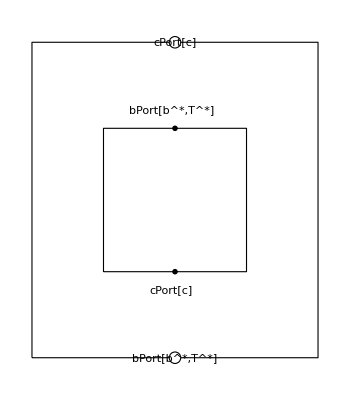

```mathematica
DiagramFlip@Diagram[A,b,c,"PortArrows"->{Placed[Red,None],Red}]//DiagramGrid
```

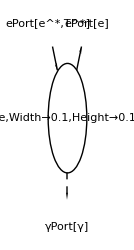

```mathematica
Diagram[A,{e,SuperStar[e]},γ,"Shape"->"Circle","Width"->.1,"Height"->.1,"PortArrows"->{Automatic,Dashed}]
```

```mathematica
ColumnDiagram[{
Diagram["in",{e,SuperStar[e]},"Shape"->None],
Diagram[A,{e,SuperStar[e]},γ,"Shape"->"Circle","Width"->.1,"Height"->.1,"PortArrows"->{Automatic,Dashed}],
Diagram["out",γ,{},"Shape"->None,Alignment->Center]
},"Rotate"->Right,"WireArrows"->True]
```

-Graphics-

```mathematica
DiagramComposition[Diagram[B,{c,SuperStar[a],b},{},"PortArrows"->{{Cyan,Magenta,Yellow}}],Diagram[A,{},{SuperStar[a],b,c},"PortArrows"->{{Red,Green,Blue}}]]
```

-Graphics-

```mathematica
DiagramComposition[Diagram[B,{SuperStar[a],b},{},"PortArrows"->{{Cyan,Magenta}}],Diagram[A,{},{SuperStar[a],b,c},"PortArrows"->{{Red,Green,Blue}}]]
```

-Graphics-

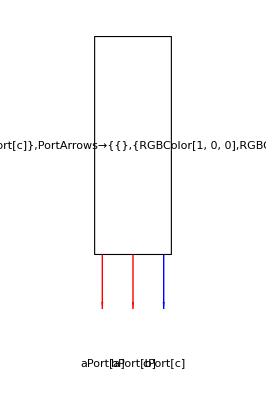

```mathematica
Diagram["A",{a⊗b,c},"PortArrows"->{{Red,Blue}}]["Flatten"]
```

```mathematica
DiagramNetwork[Diagram["A",SuperStar[a],b],Diagram[B,SuperStar[a]]]
```

-Graphics-

```mathematica
DiagramComposition[Diagram[B,{c,SuperStar[a],b},{},"PortArrows"->{{Cyan,Magenta,Yellow}}],Diagram[A,{},{b,SuperStar[a]},"PortArrows"->{{Red,Green}}]]
```

-Graphics-

```mathematica
DiagramComposition[Diagram[B,{c,SuperStar[a],b},{},"PortArrows"->{{Dashed,Magenta,Automatic}}],Diagram[A,{},{b,SuperStar[a]},"PortArrows"->{{Red,Green}}]]["Network"]
```

-Graphics-

```mathematica
ToDiagram[RandomGraph[{5,8}]]["Arrange"]["Network"]//SimplifyDiagram
```

-Graphics-

```mathematica
Diagram[{Diagram[A,a,a],Diagram[B,a,b]}]
```

-Graphics-

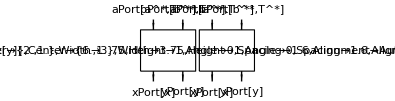

```mathematica
Diagram[Diagram[A,{a,b},{x,y}]⊗Diagram[A,{a,b},{x,y}]]//DiagramGrid
```

```mathematica
Diagram[Diagram[Diagram[A,{a,b},{x,y}]/*Diagram[B,{x,y},{s}]],{a,2},3]["Function"]
```

Sequence@@{#11}&@*B@*(Sequence@@{#11,#12}&)@*A

```mathematica
Diagram[Diagram[Diagram[A,{a,b},{x,y}]/*Diagram[B,{x,y},{s}]],{a,2},3]
```

-Graphics-

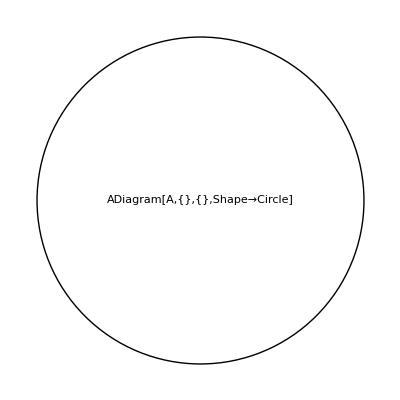
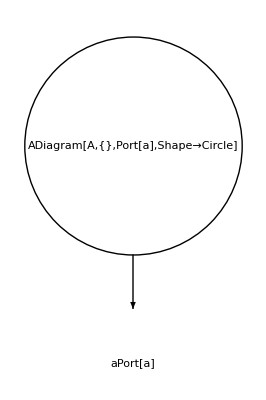
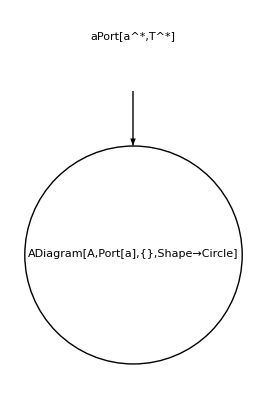
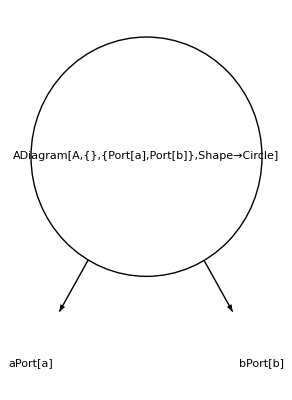
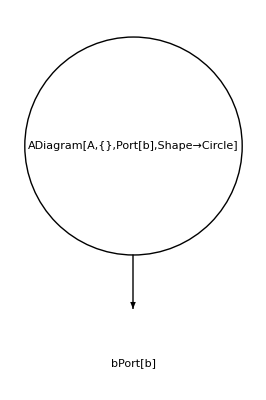
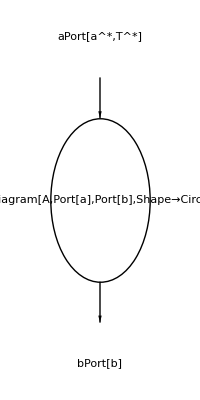
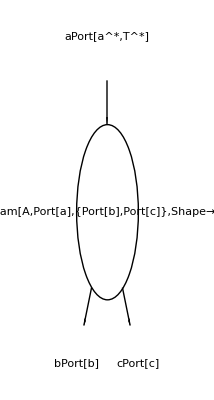
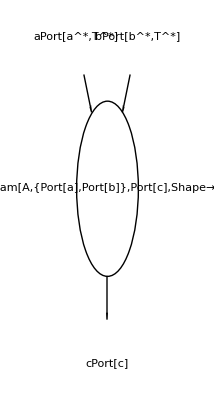

```mathematica
{Diagram[A,"Shape"->"Circle"],Diagram[A,a,"Shape"->"Circle"],Diagram[A,a,{},"Shape"->"Circle"],Diagram[A,{a,b},"Shape"->"Circle"],Diagram[A,{},b,"Shape"->"Circle"],Diagram[A,a,b,"Shape"->"Circle"],Diagram[A,a,{b,c},"Shape"->"Circle"],Diagram[A,{a,b},c,"Shape"->"Circle"],Diagram[A,{a,b},{c,d},"Shape"->"Circle"]
}
```

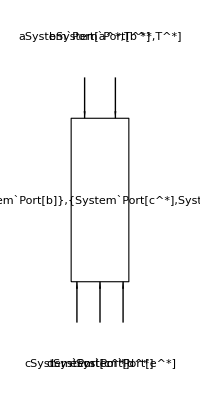

```mathematica
Diagram["A",{a,b},PortDual/@{c,d,e}]
```

```mathematica
DiagramDual[A]
```

A^*

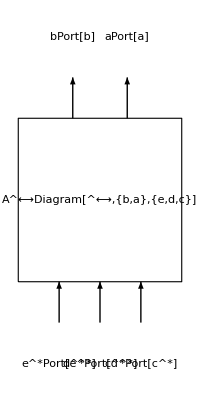

```mathematica
DiagramReverse[A]
```

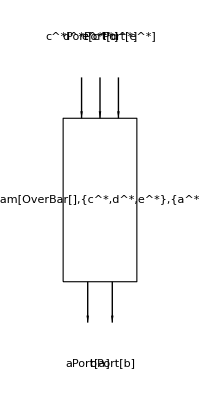

```mathematica
DiagramFlip[A]
```

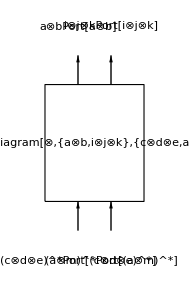

```mathematica
DiagramProduct[A,B]["HoldExpression"]//ReleaseHold
```

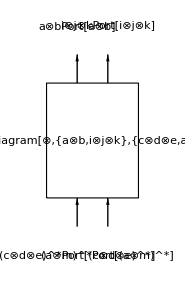
-Graphics-^⟷

```mathematica
DiagramReverse[DiagramProduct[A,B]]["Expression"]["HoldExpression"]
```

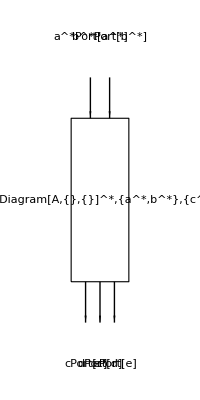

```mathematica
DiagramDual[A]
```

```mathematica
A
```

-Graphics-

```mathematica
DiagramFlip[A]
```

-Graphics-

```mathematica
DiagramFlip@DiagramReverse[A]
```

-Graphics-

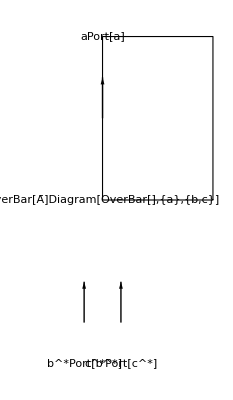

```mathematica
DiagramFlip@DiagramFlip@Diagram["A",{a},{b,c},"Shape"->Rectangle[]]
```

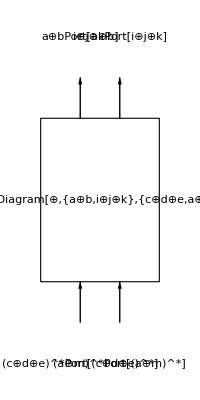

```mathematica
Diagram[A⊕B]
```

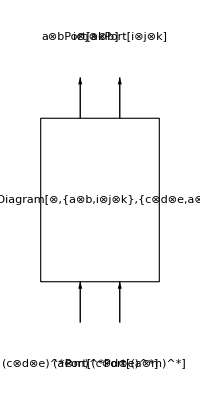

```mathematica
DiagramProduct[A,B]
```

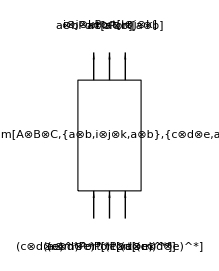

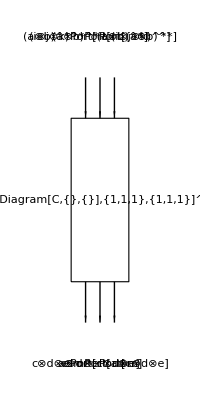

```mathematica
Diagram["A"⊗"B"⊗"C",{a⊗b,i⊗j⊗k,a⊗b},{c⊗d⊗e,a⊗m,c⊗d⊗e}]
DiagramDual[%]
```

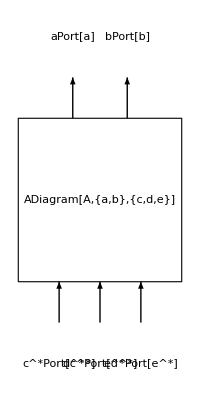
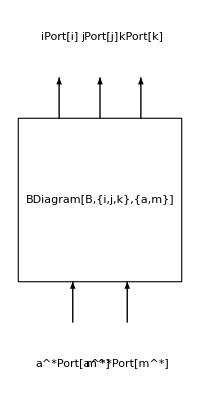
-Graphics-⊗-Graphics-⊗-Graphics-

```mathematica
DiagramProduct[A,B,A]["HoldExpression"]
```

```mathematica
Diagram[A⊕B⊕A,ImageSize->200]["HoldExpression"]
```

-Graphics-⊕-Graphics-⊕-Graphics-

```mathematica
DiagramsNetGraph[{Diagram[A⊕B⊕A,ImageSize->200]}]
```

```mathematica
Diagram[-Graphics-,{},{SuperStar[d]}]
```

```mathematica
DiagramNetwork[Diagram["A",a,a,"PortArrows"->{Red,Blue}]]["NetGraph"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",{a,b},{d},"PortArrows"->Green],Diagram["B",{c},{SuperStar[a]},"PortArrows"->Blue],Diagram["C"⊗"C",{x⊗c,x⊗SuperStar[c]},{b,SuperStar[b]},"PortArrows"->{Red}],"BinarySpiders"->True]
```

-Graphics-

```mathematica
DiagramReverse[Diagram["η",{SuperStar[1],1},"Shape"->"Wires"[{{1,2}}]]]
```

-Graphics-

```mathematica
ColumnDiagram[{DiagramProduct[Diagram["η",{SuperStar[1],1},"Shape"->"Wires"[{{1,2}}]],IdentityDiagram[{1}]],DiagramProduct[IdentityDiagram[{SuperStar[1]}],PermutationDiagram[{1,1}->{1,1},Cycles[{{1,2}}]]],DiagramProduct[Diagram["ϵ",{SuperStar[1],1},{},"Shape"->"Wires"[{{1,2}}]],IdentityDiagram[{1}]]}]
```

-Graphics-

```mathematica
DiagramProduct[Diagram["ϵ",{SuperStar[1],1},{},"Shape"->"Wires"[{{1,2}}]],IdentityDiagram[{1}]]["FlatOutputPorts"]
```

{1}

```mathematica
DiagramReverse@DiagramProduct[Diagram["ϵ",{SuperStar[1],1},{},"Shape"->"Wires"[{{1,2}}]],IdentityDiagram[{1}]]
```

-Graphics-

```mathematica
DiagramReverse[ColumnDiagram[{DiagramProduct[Diagram["η",{SuperStar[1],1},"Shape"->"Wires"[{{1,2}}]],IdentityDiagram[{1}]],DiagramProduct[IdentityDiagram[{SuperStar[1]}],PermutationDiagram[{1,1}->{1,1},Cycles[{{1,2}}]]],DiagramProduct[Diagram["ϵ",{SuperStar[1],1},{},"Shape"->"Wires"[{{1,2}}]],IdentityDiagram[{1}]]}]]
```

-Graphics-

```mathematica
DiagramSum[Diagram["η",{Port[OverBar[1]⊕1]}],IdentityDiagram[{1}]]
```

-Graphics-

#### DiagramGraph

```mathematica
DiagramNetwork[Diagram["A",b,a],Diagram["B",c,b],Diagram["C",b,a],Diagram["D",c,b]]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",b,a],Diagram["B",c,b],Diagram["C",b,a],Diagram["D",c,b]]
%["Grid","Rotate"->Right,ImageSize->Large]
```

-Graphics-

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",{a,b},d],Diagram["B",c,a],Diagram["C",{x,c},b]]
```

-Graphics-

```mathematica
DiagramNetwork[DiagramProduct[Diagram["C",c],Diagram["C",c]]]
```

-Graphics-

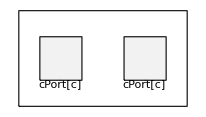

-Graphics-

```mathematica
DiagramNetwork[DiagramProduct[Diagram["C",c],Diagram["C",c]]]["Arrange","PortFunction"->Function[#["Name"]]]
DiagramNetwork[DiagramProduct[Diagram["C",c],Diagram["C",c]]]["Arrange","PortFunction"->Function[#["HoldExpression"]]]
```

```mathematica
DiagramNetwork[Diagram["A",{1,2},{3,4}],Diagram["B",{1,2},{3,4,5}]]["Arrange"]
```

-Graphics-

```mathematica
DiagramProduct[Diagram["A",a,b],DiagramComposition[Diagram["B",d,d],Diagram["C",{e,f},{f,d}]]]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["B",d,c],Diagram["C",{e,f},{f,d}]]
```

-Graphics-

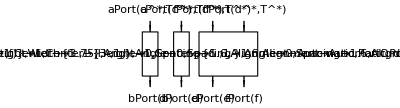

```mathematica
DiagramProduct[Diagram["A",a,b],DiagramComposition[Diagram["B",c,d],Diagram["C",{f,d},{e,f}]]]["Grid"]
```

```mathematica
ColumnDiagram[{Diagram["C",{f,d},{e,f}],Diagram["B",c,d]}]["InputPorts"]
```

{c^*,(f⊗d)^*}

```mathematica
DiagramComposition[Diagram["B",c,d],Diagram["C",{f,d},{e,f}]]["InputPorts"]
```

{c^*,f^*,d^*}

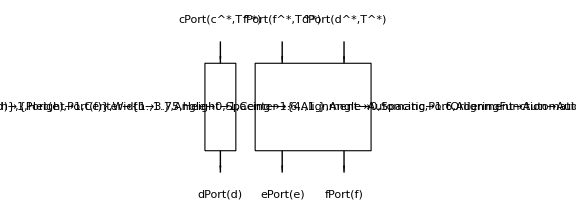

```mathematica
DiagramGrid[ColumnDiagram[{Diagram["C",{f,d},{e,f}],Diagram["B",c,d]}],ImageSize->Large]
```

```mathematica
DiagramGrid[DiagramComposition[Diagram["B",c,d],Diagram["C",{f,d},{e,f}]],ImageSize->Large]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",{a},{d},"Shape"->"Triangle"],Diagram["B",{a},{d}],Diagram["C",{c},{a}],Diagram["D",{f,a},c,"Shape"->"Circle"]]["NetGraph","BinarySpiders"->All,"RemoveCycles"->True]
```

-Graphics-

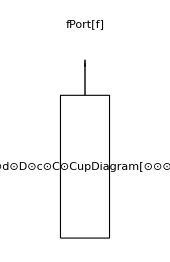

```mathematica
DiagramNetwork[Diagram["A",{a},{d},"Shape"->"Triangle"],Diagram["B",{a},{d}],Diagram["C",{c},{a}],Diagram["D",{f,a},c,"Shape"->"Circle"]]["Normal"]
```

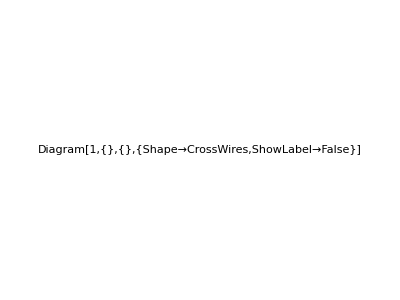
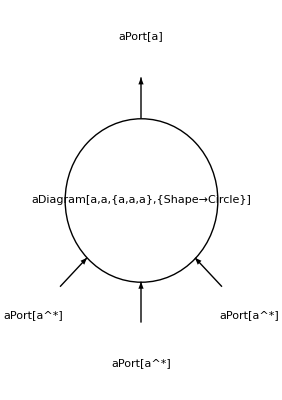
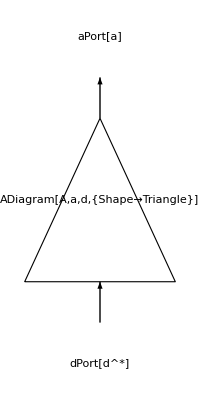
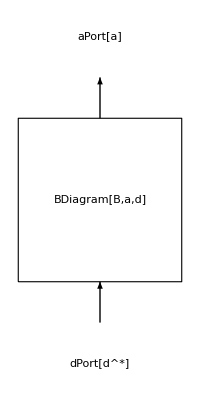
```mathematica
Extract[#,ProcessTheory`Diagram`Private`decompositionInputPositions[#]]&@CircleTimes[-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-,-Graphics-⊙(-Graphics-⊗-Graphics-⊗-Graphics-)⊙(-Graphics-⊗-Graphics-⊗-Graphics-)⊙(-Graphics-⊗-Graphics-⊗-Graphics-)⊙-Graphics-⊙(-Graphics-⊗-Graphics-)]
```

{-Graphics-,-Graphics-,-Graphics-}

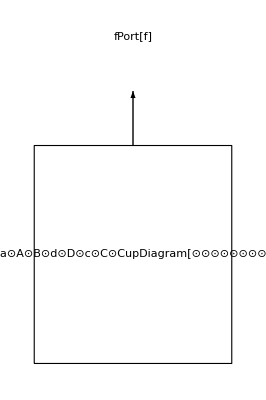

```mathematica
DiagramNetwork[Diagram["A",{a},{d},"Shape"->"Triangle"],Diagram["B",{a},{d}],Diagram["C",{c},{a}],Diagram["D",{f,a},c,"Shape"->"Circle"]]["Normal"]
```

```mathematica
DiagramNetwork[Diagram["A",{a},{d},"Shape"->"Triangle"],Diagram["B",{a},{d}],Diagram["C",{c},{a}](*,Diagram["D",{f,a},c,"Shape"->"Circle"]*)]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",{a},{d},"Shape"->"Triangle"],Diagram["B",{a},{d}],Diagram["C",{c},{a}],Diagram["D",{f,a},c,"Shape"->"Circle"]]
```

-Graphics-

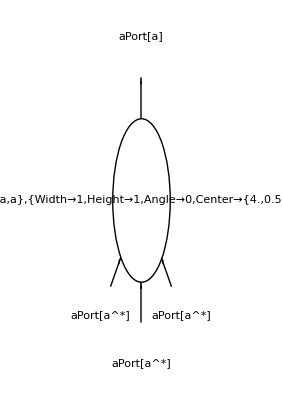
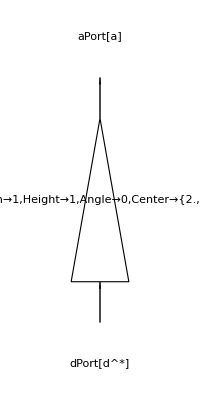
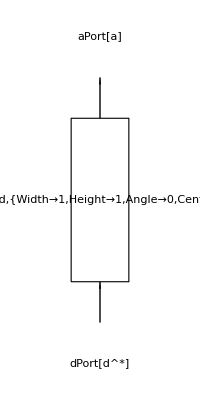
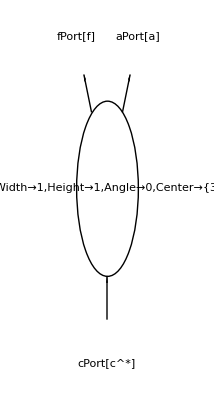
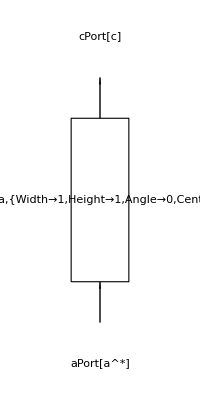
-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-

```mathematica
DiagramNetwork[Diagram["A",a,d,"Shape"->"Triangle"],Diagram["B",a,d],Diagram["C",{c},{a}],Diagram["D",{f,a},c,"Shape"->"Circle"]]["Normal"]["Decompose"]
```

```mathematica
DiagramColumn[{-Graphics-,-Graphics-},"PortFunction"->(#["HoldExpression"]&)]["Grid"]
```

-Graphics-

```mathematica
DiagramColumn[{-Graphics-,-Graphics-},"PortFunction"->(#["HoldExpression"]&)]["Normal"]["Grid"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",a,d,"Shape"->"Triangle"],Diagram["B",a,d],Diagram["C",{c},{a}],Diagram["D",{f,a},c,"Shape"->"Circle"]]["Grid"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",a,d,"Shape"->"Triangle"],Diagram["B",a,d],Diagram["C",{c},{a}],Diagram["D",{f,a},c,"Shape"->"Circle"]]["Decompose"]
```

(-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊗-Graphics-⊙(-Graphics-⊗-Graphics-)⊙(-Graphics-⊗-Graphics-⊗-Graphics-)⊙(-Graphics-⊗-Graphics-)⊙-Graphics-⊙(-Graphics-⊗-Graphics-))⊙-Graphics-⊙(-Graphics-⊗-Graphics-)⊙(-Graphics-⊗-Graphics-)⊙(-Graphics-⊗-Graphics-)⊙-Graphics-

```mathematica
DiagramNetwork[Diagram["A",a,d,"Shape"->"Triangle"],Diagram["B",a,d],Diagram["C",{c},{a}],Diagram["D",{f,a},c,"Shape"->"Circle"]]["Grid","WireArrows"->False,"PortLabels"->None,"HorizontalGapSize"->0,"Rotate"->Right,"Outline"->None,ImageSize->Medium]
```

-Graphics-

```mathematica
DiagramNetwork[-Graphics-,-Graphics-,-Graphics-]["NetGraph"]
```

-Graphics-

```mathematica
diag=DiagramNetwork[Diagram["A",{a},{d},"Shape"->"Triangle"],Diagram["B",{a},{d}],Diagram["C",{c},{a}],Diagram["D",{f,a},c,"Shape"->"Circle"],Diagram["E",e,e]]
```

-Graphics-

```mathematica
diag["Graph"]
```

```mathematica
DiagramNetwork[Diagram["A",a,b],Diagram["B",a,c]]["Arrange"]["Name"]
```

a⊙π⊙(1⊗B)⊙π⊙(1⊗A)

```mathematica
DiagramProduct[Diagram["A",a,b],Diagram["A",a,b]]["SubDiagrams"]
```

{-Graphics-,-Graphics-}

```mathematica
x=Diagram["X",{c,d},"Shape"->"UpsideDownTriangle","Width"->2]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["Y",a,d],x]["Grid",Dividers->True]
```

-Graphics-

```mathematica
DiagramComposition[DiagramFlip@Diagram["X",{a,b},d],DiagramNetwork[DiagramProduct[Diagram["A",a,b],Diagram["C",d,e]],Diagram["B",a,c]]]["Grid",Dividers->All,ImageSize->Medium]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",a,b],Diagram["B",a,c],Diagram["C",a,c]]["Grid"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",{a,b},b],Diagram["B",a,c]]["Grid",ImageSize->Large,"Rotate"->Right,"HorizontalGapSize"->0]
```

-Graphics-

```mathematica
DiagramNetwork[-Graphics-,-Graphics-,-Graphics-]["Grid",ImageSize->Large,"Rotate"->Right]
```

-Graphics-

```mathematica
diag["Grid","PortLabels"->None,ImageSize->Large,"Rotate"->Up]
```

-Graphics-

```mathematica
diag["Graph"]
```

-Graphics-

```mathematica
DiagramColumn[{Diagram["A",a,f],diag}]["Grid"]
```

-Graphics-

```mathematica
DiagramColumn[{Diagram["A",a,f],diag}]
```

-Graphics-

```mathematica
DiagramColumn[{Diagram["A",a,f],diag}]
```

-Graphics-

```mathematica
DiagramColumn[{Diagram["A",a,f],diag}]["Arrange"]
```

-Graphics-

```mathematica
DiagramProduct[Diagram["F",a,d,"Shape"->"Triangle"],DiagramColumn[{Diagram["A",a,f],diag}]]["Grid"]
```

-Graphics-

```mathematica
DiagramProduct[Diagram["F",a,d,"Shape"->"Triangle"],DiagramColumn[{Diagram["A",a,f],diag}]]["Arrange"]["ArraySymbol"]
```

(Fad.1dd.1dd.1dd.1dd.1dd.1dd.1dd.1dd.1dd.1dd.1dd.1dd.1dd.1dd.1dd)⊗(Aaf.(1ff.1ff.1ff.1ff.1ff.1ff)⊗(Capaa.a4aaaa⊗1aa.14aaaa⊗Aad⊗1aa.Bad⊗16adaada.π8dadaaadd.14aaaa⊗ddd).π6faaafa.1aa⊗D3fac.1aa⊗ccc.1aa⊗Cca.Cupaa.Capee.eee⊗1ee.Eee⊗1ee.(-Graphics-)^⟷ee)

```mathematica
DiagramProduct[Diagram["F",a,d,"Shape"->"Triangle"],DiagramColumn[{Diagram["A",a,f],diag}]]["Grid",Dividers->True,"Outline"->True,"PortLabels"->Automatic,"WireArrows"->True,Alignment->Center,ImageSize->Large]
```

-Graphics-

```mathematica
Diagram["Cup",{SuperStar[e],e},{},"PortLabels"->{Placed[Automatic,{-2/3,1}],Automatic},"PortArrows"->{None,Automatic},"Width"->7.5,"Height"->1,"Center"->{8.,-31.5},"Angle"->0,Alignment->Center,"Shape"->"Wire","ShowLabel"->False]
```

-Graphics-

```mathematica
diag["SubDiagrams"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
diag["NetGraph","BinarySpiders"->True,"UnarySpiders"->True]
```

-Graphics-

```mathematica
diag
```

-Graphics-

```mathematica
DiagramColumn[{Diagram["A",{},f],diag}]["Grid"]
```

-Graphics-

```mathematica
diag["Grid"]
```

-Graphics-

```mathematica
diag["Grid"]
```

-Graphics-

```mathematica
g=DiagramsNetGraph[diag["SubDiagrams"],"BinarySpiders"->All,"RemoveCycles"->True]
```

-Graphics-

```mathematica
hvm
```

<|S→NET[CON[a,CON[CON[a,b],CON[ERA[*],b]]],{}],Z→NET[CON[ERA[*],CON[a,a]],{}],decode→NET[CON[CON[REF[decode__C0],CON[NUM[0],a]],a],{}],decode__C0→NET[CON[OPR[NUMOP[ADD,{1}],a],a],{}],encode→NET[CON[SWI[CON[CON[ERA[*],CON[a,a]],REF[encode__C0]],b],b],{}],encode__C0→NET[CON[a,CON[DUP[CON[d,e],b],CON[c,e]]],{REDEX[True,REF[encode],CON[a,CON[b,CON[c,d]]]]}],main→NET[c,{REDEX[True,REF[S],CON[b,c]],REDEX[True,REF[S],CON[a,b]],REDEX[True,REF[S],CON[REF[Z],a]]}],mul→NET[CON[CON[b,c],CON[CON[a,b],CON[a,c]]],{}]|>

```mathematica
ExpressionTree/@hvm
```

<|decode→-Graphics-,decode__C0→-Graphics-,encode→-Graphics-,encode__C0→-Graphics-,main→-Graphics-,mul→-Graphics-|>

main = (decode (mul (encode 3) (encode 2)))

@main = d
  & @decode ~ (c d)
  & @mul ~ (a (b c))
  & @encode ~ (3 a)
  & @encode ~ (2 b)

```mathematica
"NET"["d",{"REDEX"[True,"REF"["decode"],"CON"["c","d"]],"REDEX"[True,"REF"["mul"],"CON"["a","CON"["b","c"]]],"REDEX"[True,"REF"["encode"],"CON"["NUM"["3"],"a"]],"REDEX"[True,"REF"["encode"],"CON"["NUM"["2"],"b"]]}]
-Graphics-
```

```mathematica
HVMToDiagrams[hvm]
```

<|decode→NET[CON[CON[REF[decode__C0],CON[NUM[0],a]],a],{}],decode__C0→NET[CON[OPR[NUMOP[ADD,{1}],a],a],{}],encode→NET[CON[SWI[CON[CON[ERA[*],CON[a,a]],REF[encode__C0]],b],b],{}],encode__C0→NET[CON[a,CON[DUP[CON[d,e],b],CON[c,e]]],{REDEX[True,REF[encode],CON[a,CON[b,CON[c,d]]]]}],main→NET[d,{REDEX[True,REF[decode],CON[c,d]],REDEX[True,REF[mul],CON[a,CON[b,c]]],REDEX[True,REF[encode],CON[NUM[0],a]],REDEX[True,REF[encode],CON[NUM[0],b]]}],mul→NET[CON[CON[b,c],CON[CON[a,b],CON[a,c]]],{}]|>

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
ProcessDiagram[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]["Graph",VertexLabels->_->None,VertexSize->_->1]
```

-Graphics-

```mathematica
ClearPorts[]
diagrams=DiagramNetwork@@@HVMToDiagrams/@hvm
```

<|S→-Graphics-,Z→-Graphics-,decode→-Graphics-,decode__C0→-Graphics-,encode→-Graphics-,encode__C0→-Graphics-,main→-Graphics-,mul→-Graphics-|>

```mathematica
diagrams["S"]["Graph","ShowWireLabels"->False,VertexLabels->_->None]
```

-Graphics-

```mathematica
diagrams["S"]["Grid","PortLabels"->False,"Rotate"->Up,(*"ShowLabel"->True,*)Dividers->True,ImageSize->Large,"Outline"->False,Alignment->Left]
```

-Graphics-

```mathematica
Nest[Not,True,10^8]//AbsoluteTiming
```

{6.22312,True}

```mathematica
diagrams
```

<|S→-Graphics-,Z→-Graphics-,decode→-Graphics-,decode__C0→-Graphics-,encode→-Graphics-,encode__C0→-Graphics-,main→-Graphics-,mul→-Graphics-|>

```mathematica
Diagram["1",{a,a},{a,a},"Angle"->Pi/2,Alignment->Left,"ShowLabel"->False]
```

-Graphics-

```mathematica
DiagramNetwork[-Graphics-,-Graphics-,-Graphics-]["Grid","Outline"->True]
```

-Graphics-

```mathematica
#["Grid","PortLabels"->False,"Outline"->True,Dividers->All,ImageSize->Medium,Alignment->Left]&/@diagrams
```

<|S→-Graphics-,Z→-Graphics-,decode→-Graphics-,decode__C0→-Graphics-,encode→-Graphics-,encode__C0→-Graphics-,main→-Graphics-,mul→-Graphics-|>

```mathematica
Diagram["1",{vd$11},{vd$11},{"PortLabels"->{Placed[Automatic,{-2/3,1}],Automatic},"PortArrows"->{None,Automatic},"Width"->1,"Height"->1,"Angle"->0,"Center"->{13.,-39.5},"Shape"->"CrossWires","ShowLabel"->False}]
```

```mathematica
DiagramsNetGraph[#,"ShowPortLabels"->False,"ShowWireLabels"->False,ImageSize->Large]&/@diagrams
```

<|decode→-Graphics-,decode__C0→-Graphics-,encode→-Graphics-,encode__C0→-Graphics-,main→-Graphics-,mul→-Graphics-|>

```mathematica
DiagramsGraph[diagrams["main"]]
```

-Graphics-

```mathematica
DiagramsNetGraph[diagrams["main"],"ShowPortLabels"->False,"ShowWireLabels"->False]
```

-Graphics-

#### DiagramCircuit

```mathematica
<<ProcessTheory`Circuit`
```

```mathematica
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`DiagramPlot`
```

```mathematica
Diagram[Diagram[Subscript["C", "NOT"][{1},{}],{1,2},{1,2}]⊙Diagram["SWAP",{2,3},{2,3}]]
```

-Graphics-

```mathematica
DiagramProduct[Diagram[A,1,2],Diagram[B,3,{4,5}]]["FlattenOutputs"]
```

-Graphics-

```mathematica
ToDiagram[QuantumCircuitOperator["Fourier"[2]]]["Arrange"]
```

-Graphics-

```mathematica
ToDiagram[QuantumCircuitOperator["Fourier"[2]]]["Grid"]
```

-Graphics-

```mathematica
ToDiagram[QuantumCircuitOperator["Fourier"[3]]]["Grid"]
```

-Graphics-

```mathematica
DiagramsToCircuitDiagram@Reverse@ToDiagram[QuantumCircuitOperator["Fredkin"]]["SubDiagrams"]/.Interpretation[_,qo_QuantumOperator]:>RuleCondition@qo["Label"]
```

<|Elements→{<|Type→Operator,Label→C_NOT[{3},{}],Thickness→{{2,2},{2,2}},Position→{{2,3},{2,3}},Thick→False,Diagram→None|>,<|Type→Operator,Label→H,Thickness→{{2},{2}},Position→{{3},{3}},Thick→False,Diagram→None|>,<|Type→Operator,Label→T,Thickness→{{2},{2}},Position→{{1},{1}},Thick→False,Diagram→None|>,<|Type→Operator,Label→T,Thickness→{{2},{2}},Position→{{2},{2}},Thick→False,Diagram→None|>,<|Type→Operator,Label→T,Thickness→{{2},{2}},Position→{{3},{3}},Thick→False,Diagram→None|>,<|Type→Operator,Label→C_NOT[{2},{}],Thickness→{{2,2},{2,2}},Position→{{1,2},{1,2}},Thick→False,Diagram→None|>,<|Type→Operator,Label→C_NOT[{3},{}],Thickness→{{2,2},{2,2}},Position→{{2,3},{2,3}},Thick→False,Diagram→None|>,<|Type→Operator,Label→C_NOT[{1},{}],Thickness→{{2,2},{2,2}},Position→{{1,3},{1,3}},Thick→False,Diagram→None|>,<|Type→Operator,Label→T^†,Thickness→{{2},{2}},Position→{{2},{2}},Thick→False,Diagram→None|>,<|Type→Operator,Label→C_NOT[{1},{}],Thickness→{{2,2},{2,2}},Position→{{1,2},{1,2}},Thick→False,Diagram→None|>,<|Type→Operator,Label→T^†,Thickness→{{2},{2}},Position→{{1},{1}},Thick→False,Diagram→None|>,<|Type→Operator,Label→T^†,Thickness→{{2},{2}},Position→{{2},{2}},Thick→False,Diagram→None|>,<|Type→Operator,Label→T,Thickness→{{2},{2}},Position→{{3},{3}},Thick→False,Diagram→None|>,<|Type→Operator,Label→C_NOT[{3},{}],Thickness→{{2,2},{2,2}},Position→{{2,3},{2,3}},Thick→False,Diagram→None|>,<|Type→Operator,Label→C_NOT[{1},{}],Thickness→{{2,2},{2,2}},Position→{{1,3},{1,3}},Thick→False,Diagram→None|>,<|Type→Operator,Label→H,Thickness→{{2},{2}},Position→{{3},{3}},Thick→False,Diagram→None|>,<|Type→Operator,Label→C_NOT[{2},{}],Thickness→{{2,2},{2,2}},Position→{{1,2},{1,2}},Thick→False,Diagram→None|>,<|Type→Operator,Label→C_NOT[{3},{}],Thickness→{{2,2},{2,2}},Position→{{2,3},{2,3}},Thick→False,Diagram→None|>},Label→None,Expand→True|>

```mathematica
DiagramPlot[DiagramsToCircuitDiagram@Reverse@ToDiagram[QuantumCircuitOperator["Fredkin"]]["SubDiagrams"]/.qo_QuantumOperator:>qo["Label"]]
```

-Graphics-

```mathematica
DiagramsToCircuitDiagram[{Diagram["H",{1},{1}],Diagram["C"[{1},{}],{1,2},{1,2}],Diagram["SWAP",{2,3},{2,3}],Diagram[Diagram["C"[{1},{}],{1,2},{1,2}]⊙Diagram["SWAP",{2,3},{2,3}]]}]
DiagramPlot[%,"Expand"->2]
```

<|Elements→{<|Type→Operator,Label→H,Thickness→{{2},{2}},Position→{{1},{1}},Thick→False,Diagram→None|>,<|Type→Operator,Label→C[{1},{}],Thickness→{{2,2},{2,2}},Position→{{1,2},{1,2}},Thick→False,Diagram→None|>,<|Type→Operator,Label→SWAP,Thickness→{{2,2},{2,2}},Position→{{2,3},{2,3}},Thick→False,Diagram→None|>,<|Type→Diagram,Label→-Graphics-,Thickness→{{2,2,2},{2,2,2}},Position→{{1,2,3},{2,3,1}},Thick→False,Diagram→<|Elements→{<|Type→Operator,Label→C[{1},{}],Thickness→{{2,2},{2,2}},Position→{{1,2},{1,2}},Thick→False,Diagram→None|>,<|Type→Operator,Label→SWAP,Thickness→{{2,2},{2,2}},Position→{{2,3},{2,3}},Thick→False,Diagram→None|>},Label→None,Expand→True|>|>},Label→None,Expand→True|>

-Graphics-

```mathematica
QuantumCircuitOperator[{"Cup"->{2,3},"Permutation"->{1,2,3}->{3,1,2},"Cap","I"->3->10}]
```

-Graphics-

#### Diagram composition

```mathematica
DiagramComposition[Diagram[1+1,{a,b},{SuperStar[c]}],Diagram["B",{c,d},{SuperStar[e]}]]
```

-Graphics-

```mathematica
Diagram["A",a,b,"Width"->2,"Center"->{2,2}]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram["A",{a},{b,x,c}],Diagram["B",{c,b},{d}]}]
```

-Graphics-

```mathematica
DiagramDecompose@DiagramCompose[{Diagram["A",a,{b,x,c}],Diagram["B",{c,b},d]}]
```

-Graphics-⊙-Graphics-⊙(-Graphics-⊗-Graphics-)

```mathematica
DiagramComposition[Diagram["A",a,{b,x,c}],Diagram["B",{c,b},d]]
```

-Graphics-

```mathematica
Diagram[DiagramCompose[{Diagram["A",a,{b,x,c}],Diagram["B",{c,b},d]}],"Width"->2]
```

-Graphics-

```mathematica
Graph[{1,2,3,4,5,6,6},{1<->5,2<->4,3<->4,4<->5,4<->6,6<->7},VertexLabels->{1->None,2->None,3->None,4->g,5->f,6->h,7->None},EdgeLabels->{1<->5->A,2<->4->B,3<->4->C,4<->5->A,4<->6->D,6<->7->A},VertexShapeFunction->{1|2|3|7->None}]
```

-Graphics-

```mathematica
DiagramsGraph[{Diagram["g",{},{b,c,a,d}],Diagram["f",a,a],Diagram["h",d,a]}]
```

-Graphics-

```mathematica
Diagram[-Graphics-,{},{SuperStar[b],SuperStar[c]}]
```

```mathematica
DiagramNetwork[Diagram["g",{},{b,c,a,d}],Diagram["f",a,a],Diagram["h",d,a]]
```

-Graphics-

#### Diagram sum

```mathematica
DiagramProduct[Diagram[A,a,b],Diagram[B,a,b]]["Grid","Frames"->All]
```

-Graphics-

```mathematica
DiagramSum[Diagram[A,a,b],Diagram[B,c,d]]["Grid"]
```

-Graphics-

```mathematica
DiagramComposition[Diagram[C,b⊕b,c],DiagramSum[Diagram[A,a,b],Diagram[B,a,b]]]["Grid"]
```

-Graphics-

#### Diagram grid

```mathematica
Diagram[A,Port[a],Port[c],"PortLabels"->{{Automatic},{Placed[Automatic,{-2/3,1}]}},"PortArrows"->{{Automatic},{Placed[None,Automatic]}},"Center"->{1.,5.},"Width"->1,"Height"->1,"Angle"->0,"Spacing"->1.6,Alignment->Automatic,"PortOrderingFunction"->Automatic]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram[A,a,b,"PortArrows"->Blue],Diagram[A,a,c]}]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram[A,a,b,"PortArrows"->Blue],Diagram[B,a,c],Diagram[C,{c,b},d,"PortArrows"->{{Inherited,Cyan},Red}]},"Frames"->All]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram[A,a,b,"PortArrows"->Blue],Diagram[B,a,c],Diagram[C,{b,e},{d,c},"PortArrows"->{{Inherited,Cyan},Red}]}]["Grid"]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["A",{b,x,c},a,"Height"->1,"Width"->2],Diagram["B",d,{c,b}],Diagram["C",e,{d,x},Alignment->Scaled[0.25],"Height"->2],Diagram["D",e,Alignment->Left]]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram["A",a,{b,c,d}],Diagram["B",{d,b},x]}]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",a,b],Diagram["B",a,b]]["Grid"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",a,b],Diagram["B",x,b],Diagram["C",a,b]]["Grid","NetworkMethod"->"Foliation"]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["g",{a,d},{x}],DiagramProduct[DiagramComposition[Diagram["A",b,a],Diagram["B",c,b]],Diagram["h",e,d]],Diagram["i",{c,e}]]["Grid"]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["g",{a,d},{x}],DiagramProduct[DiagramComposition[Diagram["A",b,a],Diagram["B",c,b]],Diagram["h",e,d]],Diagram["i",{c,e}]]["Network"]
```

-Graphics-

{d^*}

```mathematica
ColumnDiagram[{Diagram[A,a,{b,c,d}],Diagram[B,{b,d},e]}]
```

-Graphics-

```mathematica
Diagram[A,{a,b,c},"Spacing"->.1]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,{a,b,c}],Diagram[B,{c,b,y}]]["Decompose"]
```

{-Graphics-,-Graphics-}

```mathematica
SequenceAlignment[{1,1},{1,2,3,1}]
```

{{1},{{},{2,3}},{1}}

```mathematica
SequenceAlignment[{HoldForm[{2, 2, 1}], HoldForm[{1, 2, 3}]}, {HoldForm[{2, 2, 1}], HoldForm[{2, 2, 2}], HoldForm[{2, 2, 3}], HoldForm[{1, 2, 1}], HoldForm[{1, 2, 2}], HoldForm[{1, 2, 3}]}]
```

{{{2,2,1}},{{},{{2,2,2},{2,2,3},{1,2,1},{1,2,2}}},{{1,2,3}}}

```mathematica
DiagramNetwork[Diagram[A,{a,b,c},{}],Diagram[B,{c,b,y},{}]]["Grid"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,{a,b,c}],Diagram[B,{c,b,y}]]["Arrange","Direction"->Down]["Decompose"]
```

{(-Graphics-⊗-Graphics-⊗-Graphics-)⊙-Graphics-⊙(-Graphics-⊗-Graphics-)}

```mathematica
DiagramNetwork[Diagram[A,{a,b,c}],Diagram[B,{c,b,y}]]["Grid","Direction"->Down]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,{a,b,c}],Diagram[B,{c,b,y}]]["Grid",Dividers->True,"Direction"->Up]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,{a,b,c}],Diagram[B,{c,b,y}]]["Grid",Spacings->1.4]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,{a,b,c}],Diagram[B,{c,b,y}]]["Grid",Dividers->All]
```

-Graphics-

```mathematica
Diagram["π",{a,c,b},{b,a,c},"Shape"->"Wires","ShowLabel"->False]
```

-Graphics-

```mathematica
Catenate@Diagram["π",{a,b},{a},"Shape"->"Wire","ShowLabel"->False]["PortArrows"]
```

{{{-0.266667,0.5},{-0.266667,0.75}},{{0.266667,0.5},{0.266667,0.75}},{{0.,-0.5},{0.,-0.75}}}

```mathematica
Diagram["π",{a,b,c},{c,a,b},"Shape"->"Wire","ShowLabel"->False]
```

-Graphics-

```mathematica
ProcessTheory`Utilities`piDiagram[{a,b,c},{c,a,b}]
```

Diagram[Association[DiagramOptions -> {Shape -> CrossWires, ShowLabel -> False}, Expression :> Interpretation[π, Cycles[{{1, 2, 3}}]], 
   InputPorts -> {Port[Association[Expression :> PortDual[a], Type -> SuperStar[T]]], Port[Association[Expression :> PortDual[b], Type -> SuperStar[T]]], 
     Port[Association[Expression :> PortDual[c], Type -> SuperStar[T]]]}, OutputPorts -> {Port[Association[Expression :> c, Type -> T]], Port[Association[Expression :> a, Type -> T]], 
     Port[Association[Expression :> b, Type -> T]]}]]

```mathematica
DiagramNetwork[Diagram[A,{a,b,c}],Diagram[B,{c,x,y}]]["Grid","Outline"->True,ImageSize->Medium]
```

-Graphics-

```mathematica
Diagram["π",{c,x,y,a,b,c},{x,y,a,b,c,c},"PortLabels"->{None,Placed[Automatic,{-2/3,1}]},"PortArrows"->None,"Width"->8.75,"Height"->1,"Center"->{6.,3.},"Angle"->0,Alignment->Automatic,"Shape"->"CrossWires","ShowLabel"->False]
```

```mathematica
Diagram[c,{c,c},{},"PortLabels"->{None,Automatic},"PortArrows"->{None,Automatic},"Width"->3.75,"Height"->1,"Center"->{10.,1.},"Angle"->0,Alignment->Automatic,"Shape"->"Wire","ShowLabel"->False]
```

```mathematica
RowDiagram[{DiagramComposition[Diagram["A",a,b],Diagram["B",b,c]],Diagram["h",d,e]}]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["g",{a,d,f},{}],RowDiagram[{DiagramComposition[Diagram["A",b,a],Diagram["B",c,b]],Diagram["h",e,d]}],Diagram["i",{c,e}]]
%["Grid",ImageSize->Medium]
```

-Graphics-

-Graphics-

```mathematica
DiagramColumn[{Diagram["A",a,{b,x,c}],Diagram["B",{c,b},d],Diagram["C",{x,d},e]}]
%["Decompose"]
```

-Graphics-

-Graphics-⊙-Graphics-⊙(-Graphics-⊗-Graphics-)⊙-Graphics-

```mathematica
diagram=Diagram[Diagram["A",a,b]⊗Diagram["B",c,d]⊙Diagram["C",d,e]]
```

-Graphics-

```mathematica
diagram["Arrange"]
```

-Graphics-

```mathematica
diagram["Grid"]
```

-Graphics-

```mathematica
Diagram["A",a,{b,x,c}]
```

-Graphics-

```mathematica
DiagramReverse[Diagram["A",a,{b,x,c}],"Width"->2]
```

-Graphics-

```mathematica
DiagramGrid[ColumnDiagram[Reverse@{DiagramReverse@Diagram["A",{b,x,c},a,"Shape"->"Triangle"],Diagram["B",d,{c,b}],Diagram["C",e,{d,x}]}],ImageSize->Large,"Rotate"->Right]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["A",a,{b,x,c},"Shape"->"Triangle","Angle"->Pi/4],Diagram["B",{c,b},d],Diagram["C",{d,x},e]]
```

-Graphics-

```mathematica
DiagramComposition[{Diagram["A",a,{b,x,c},"Shape"->"Triangle","Angle"->Pi/4],Diagram["B",{c,b},d],Diagram["C",{d,x},e]}]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["B",c,d],Diagram["C",d,e]]//DiagramGrid
```

-Graphics-

```mathematica
Diagram["A",a,b]
DiagramComposition[Diagram["B",c,d],Diagram["C",d,e]]
```

-Graphics-

-Graphics-

```mathematica
DiagramCompose[{Diagram["A",a,b],DiagramComposition[Diagram["B",c,d],Diagram["C",d,e]]}]
```

-Graphics-

```mathematica
DiagramCompose[{Diagram["A",a,b],Diagram["B",b,c]}]
```

-Graphics-

```mathematica
DiagramJoin[{Diagram["A",a,b],Diagram["B",b,c]}]
```

-Graphics-

```mathematica
Quit
```

```mathematica
DiagramComposition[Diagram["A",a,b],DiagramComposition[Diagram["B",c,d],Diagram["C",d,e]]]
%["Arrange"]
%["Grid"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
DiagramComposition[Diagram["A",a,b],DiagramComposition[Diagram["B",c,d],Diagram["C",d,e]]]
```

-Graphics-

```mathematica
DiagramArrange[{Diagram["A",a,b],Diagram["B",b,c]}]
```

DiagramArrange[{-Graphics-,-Graphics-}]

```mathematica
DiagramComposition[Diagram["A",a,b],DiagramComposition[Diagram["B",c,d],Diagram["C",d,{e,f}]]]
DiagramGrid[%,"VerticalGapSize"->1,"HorizontalGapSize"->2,ImageSize->Medium]
```

-Graphics-

-Graphics-

```mathematica
TensorContract[TensorProduct[MatrixSymbol["A",{a,b}],MatrixSymbol["B",{a,b}]],{{1,3},{2,4}}]
```

TensorContract[Aab⊗Bab,{{1,3},{2,4}}]

```mathematica
DiagramNetwork[Diagram["A",a,b],DiagramComposition[Diagram["B",{a,c},d],Diagram["C",{d,e}]]]
```

-Graphics-

```mathematica
DiagramComposition[DiagramComposition[Diagram["A",a,b],Diagram["B",b,c]],DiagramProduct[Diagram["C",c],Diagram["D",D]]]
```

-Graphics-

```mathematica
DiagramGrid[DiagramComposition[DiagramComposition[Diagram["A",a,b],Diagram["B",b,c]],DiagramProduct[Diagram["C",c],Diagram["D",D]]],Dividers->All]
```

-Graphics-

```mathematica
DiagramGrid@DiagramComposition[Diagram["g",{x},{a,d}],DiagramProduct[DiagramComposition[Diagram["A",a,b],Diagram["B",b,c]],Diagram["h",d,e]],Diagram["i",{c,e}]]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["A",a,{b,x,c},"Height"->1],Diagram["B",{c,b},d],Diagram["C",{d,x},e,Alignment->Scaled[0.25],"Height"->2],Diagram["D",e,Alignment->Right]]["Network","ShowWireLabels"->True]
DiagramComposition[Diagram["X",y,a],%]["Network"]
DiagramComposition[Diagram["Y",z,y],%]["Network"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
DiagramGrid[DiagramComposition[Diagram["A",{b,x,c},a,"Height"->1],Diagram["B",d,{c,b}],Diagram["C",e,{d,x},Alignment->Scaled[0.25],"Height"->2],Diagram["D",e,Alignment->Center]],Dividers->All,ImageSize->Large,"VerticalGapSize"->1]
```

-Graphics-

```mathematica
DiagramGrid[DiagramProduct[Diagram["A",a,b],Diagram["A",{a,c},b],Diagram["A",a,b]],Dividers->All,"Outline"->True,ImageSize->Large,Alignment->Right,"HorizontalGapSize"->1,"VerticalGapSize"->1]
```

-Graphics-

```mathematica
DiagramGrid[DiagramComposition[Diagram["A",a,{b,x,c},"Height"->1],Diagram["B",{c,b},d],Diagram["C",{d,x},e,Alignment->Scaled[0.25],"Height"->2],Diagram["D",e,Alignment->Right]],Dividers->All,"Outline"->True,ImageSize->Large,Alignment->Center,"VerticalGapSize"->1,"HorizontalGapSize"->2]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["B",{a,c},d],Diagram["C",{d,e},"Width"->4,"Height"->2]]["Grid","Outline"->True,Alignment->Center,Dividers->True,ImageSize->Large]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["B",{a,c},d],Diagram["C",{d,e}]]["Arrange"]["ArraySymbol"]
```

Cde⊗B3dac

```mathematica
ColumnDiagram[{Diagram["C",{d,e},"PortArrows"->{Automatic,{Blue,Blue}}],Diagram["B",d,{a,c}]}]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["B",d,{a,c}],Diagram["C",{d,e}]]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",a,b],DiagramComposition[Diagram["B",{a,c},d],Diagram["C",{d,e}]]]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",a,b],DiagramComposition[Diagram["B",{a,c},d],Diagram["C",{d,e}]]]["Ports"]
```

{c,e,b}

```mathematica
Diagram[DiagramNetwork[Diagram["A",a,b],DiagramComposition[Diagram["B",{a,c},d],Diagram["C",{d,e}]]],"Angle"->0,Alignment->OptionValue[Alignment]]
```

-Graphics-

Graphics

```mathematica
DiagramNetwork[Diagram["A",a,b],DiagramComposition[Diagram["B",{a,c},d],Diagram["C",{d,e}]]]["OptionValue"["Width"]]
```

Automatic

```mathematica
DiagramNetwork[Diagram["A",a,b],DiagramComposition[Diagram["B",{a,c},d],Diagram["C",{d,e}]]]["Grid","Network"->False]
```

-Graphics-

```mathematica
DiagramComposition[Diagram["A",a,b],Diagram["B",b,{c,d}]]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram["B",b,{c,d}],Diagram["A",a,b]}]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram["A",a,b],Diagram["B",b,{c,d}]}]
```

-Graphics-

```mathematica
net=DiagramNetwork[##,"PortFunction"->(Replace[#["HoldExpression"],HoldForm[PortDual@Interpretation[HoldForm[x_Integer],_]|Interpretation[HoldForm[x_Integer],_]]:>HoldForm[x]]&)]&@@ColumnDiagram[{
DiagramProduct[Diagram["A",{1,a,2},{3,a,4}],Diagram["B",b,{2,b,5}],Diagram["C",{5,6},{4,c,6}]],
DiagramProduct[Diagram["D",{7,a,b,8},{9,d,10}],Diagram["E",{8,e},{10,11}]]}]["Network"]["SubDiagrams"]
```

-Graphics-

```mathematica
SimplifyDiagram[net]
```

-Graphics-

```mathematica
net["Graph"]//DiagramGraphSimplify//DiagramsNetGraph
```

-Graphics-

```mathematica
DiagramNetwork[##]&@@DiagramCases[ColumnDiagram[{
DiagramProduct[Diagram["A",{1,a,2},{3,a,4}],Diagram["B",b,{2,b,5}],Diagram["C",{5,6},{4,c,6}]],
DiagramProduct[Diagram["D",{7,a,b,8},{9,d,10}],Diagram["E",{8,e},{10,11}]]}],d_/;!DiagramQ[d]]//SimplifyDiagram
```

-Graphics-

#### Graph and Hypergraphs

```mathematica
g=RandomGraph[{5,7},VertexLabels->Automatic]
```

-Graphics-

```mathematica
ToDiagram[g]//DiagramDecompose//Diagram
```

-Graphics-

```mathematica
Hypergraph[{{1,2},{2,3,4},{2,5},{2,5}},EdgeLabels->{{1,2}->"A",{2,3,4}->"B"},EdgeStyle->{{2,5}->Red,{2,5}->Blue}]
```

-Graphics-

```mathematica
ToDiagram@Hypergraph[{{1,2},{2,3,4},{2,5}->tag,{2,5}},EdgeLabels->{{1,2}->"A",{2,3,4}->"B"}]
```

-Graphics-

```mathematica
hg=Hypergraph@ResourceFunction["RandomHypergraph"][{10,{{5,2},{4,3}}}]
```

-Graphics-

```mathematica
ToDiagram[hg]["Grid","NetworkMethod"->"Stratify"]
```

-Graphics-

#### NetGraph

```mathematica
Diagram[diag["Normal"]["Name"],diag["OutputPorts"],diag["InputPorts"]]
```

Diagram[Association[DiagramOptions -> {}, Expression :> HoldForm[HoldForm[Cap] ⊙ HoldForm[HoldForm[a]] ⊙ HoldForm[A] ⊙ HoldForm[B] ⊙ HoldForm[HoldForm[d]] ⊙ HoldForm[D] ⊙ 
      HoldForm[HoldForm[c]] ⊙ HoldForm[C] ⊙ HoldForm[Cup] ⊙ HoldForm[Cap] ⊙ HoldForm[HoldForm[e]] ⊙ HoldForm[E] ⊙ HoldForm[Cup]], InputPorts -> {}, 
   OutputPorts -> {Port[Association[Expression :> f, Type -> T]]}]]

```mathematica
ng=NetInitialize@NetGraph[{LinearLayer[2],ElementwiseLayer[Ramp],ThreadingLayer[Plus]},{1->2,{NetPort["Input"],2}->3}]
```

NetGraph[…]

```mathematica
ng=NetInitialize@NetGraph[{LinearLayer[2],Ramp,LinearLayer[3],SoftmaxLayer[],MeanSquaredLossLayer[]},{1->2->3->4->5},"Input"->"Scalar"]
```

NetEncoder::deprec: "NetEncoder[{Scalar,…}]" setting has been deprecated. Use ""Real" or "Integer" bare port specifications" setting instead.

NetGraph[…]

```mathematica
ToDiagram[ng,"ShowWireLabels"->False]
```

-Graphics-

```mathematica
ToDiagram[ng]["Grid","Rotate"->Right,Dividers->All]
```

-Graphics-

```mathematica
ToDiagram[ng]["Arrange"]//DiagramFunction
```

Sequence@@{#11}&@*-Graphics-@*(Apply[Sequence][{(Sequence@@{#11}&@*-Graphics-)[#1],(Sequence@@{#11}&@*({#1}&))[#2]}]&)@*(Apply[Sequence][{(Sequence@@{#11}&@*-Graphics-)[#1],(Sequence@@{#11}&@*({#1}&))[#2]}]&)@*(Apply[Sequence][{(Sequence@@{#11}&@*-Graphics-)[#1],(Sequence@@{#11}&@*({#1}&))[#2]}]&)@*(Apply[Sequence][{(Sequence@@{#11}&@*-Graphics-)[#1],(Sequence@@{#11}&@*({#1}&))[#2]}]&)

```mathematica
net=NetFlatten@NetGraph[…];
```

```mathematica
ToDiagram[net]
```

-Graphics-

```mathematica
ToDiagram[net]["Grid","Rotate"->Right,Dividers->True,"PortLabels"->False,ImageSize->Medium]
```

-Graphics-

```mathematica
NetUnfold[LongShortTermMemoryLayer[5]]
```

NetGraph[…]

```mathematica
ToDiagram[NetUnfold[LongShortTermMemoryLayer[5]]]["Grid","Rotate"->Right,"PortLabels"->False,ImageSize->Large]
```

-Graphics-

#### Lambdas

```mathematica
l=λ[λ[1[2]][λ[1[2]]]][x];
```

```mathematica
<<Wolfram`Lambda`
```

```mathematica
ToDiagram[ParseLambda["(λg. g (g λx. x)) (λh. (λf. f (f λz. z)) (h λy. y))"]]["Network","ShowPortLabels"->True]
```

-Graphics-

```mathematica
ToDiagram[ParseLambda["(λh. (λf. f (f λz. z)) (h λy. y))"]]["Grid",Dividers->All]
```

-Graphics-

```mathematica
ToDiagram[ParseLambda["(λx.x x)(λy.y)"]]["Grid",Dividers->All]
```

-Graphics-

```mathematica
ToDiagram[ParseLambda["(λx.x) X"]]
```

-Graphics-

```mathematica
ToDiagram[λ[λ[1[2]][1]][x]]
```

-Graphics-

```mathematica
NestGraph[BetaReductions,l,3,VertexShapeFunction->Function[Inset[Framed@ToDiagram[#2,PlotLabel->Column[{ColorizeLambda[#2],LambdaConvert[#2]},Alignment->Center],ImageSize->Medium](*["Grid","Rotate"->Right,"PortLabels"->False,ImageSize->Medium]*),#1,#3]],GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left},PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
ToDiagram[#,PlotLabel->Column[{LambdaSmiles[#],LambdaConvert[#]},Alignment->Center]]&/@BetaReductions[l]
```

{-Graphics-,-Graphics-}

```mathematica
ToDiagram[l]
```

-Graphics-

```mathematica
ToDiagram[λ[1]]
```

-Graphics-

```mathematica
ToDiagram[#[x]]&/@EnumerateLambdas[]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ToDiagram[l,PlotLabel->Column[{LambdaSmiles[l],LambdaConvert[l]},Alignment->Center]]
```

-Graphics-

```mathematica
l=RandomLambda[][x]
```

λ[1[λ[2[2]]]][x]

```mathematica
ToDiagram[l]
```

-Graphics-

```mathematica
ToDiagram[λ[1[x,y]]]
```

-Graphics-

#### QuantumCircuit

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
QuantumCircuitOperator["Fredkin"]
```

-Graphics-

```mathematica
ToDiagram[QuantumCircuitOperator["Fredkin"]["Sort"]]["Arrange"]["Grid","Arrange"->False,"Frames"->Automatic,Alignment->"Circuit","PortArrows"->None,"Wires"->True,"Rotate"->Pi/2]
```

-Graphics-

```mathematica
QuantumCircuitOperator["CHSH"]["Flatten"]
```

QuantumCircuitOperator[…]

```mathematica
ToDiagram[QuantumCircuitOperator["CHSH"]["Flatten"]["DiscardExtraQudits"]]["Grid",Alignment->"Circuit","Frames"->None,"Rotate"->Pi/2]
```

-Graphics-

```mathematica
ToDiagram[QuantumCircuitOperator["Fourier"]]["Network"]
```

-Graphics-

```mathematica
QuantumCircuitOperator["CHSH"][[2;;4]]
```

QuantumCircuitOperator[…]

```mathematica
ToDiagram[QuantumCircuitOperator["CHSH"][[2;;4]]]["Decompose"]/.d_Diagram:>InputForm@d["Ports"]
```

4_2[2]

1^3[2]

2^1[2]

2^2[2]

{Port[<|"Expression" :> Interpretation[1, Superscript[2, 1][2]], "Type" -> T|>], Port[<|"Expression" :> Interpretation[2, Superscript[2, 2][2]], "Type" -> T|>], Port[<|"Expression" :> PortDual[Interpretation[1, Subscript[2, 1][2]]], "Type" -> SuperStar[T]|>], Port[<|"Expression" :> PortDual[Interpretation[2, Subscript[2, 2][2]]], "Type" -> SuperStar[T]|>]}⊙{Port[<|"Expression" :> Interpretation[2, Subscript[4, 2][2]], "Type" -> T|>], Port[<|"Expression" :> Interpretation[3, Superscript[1, 3][2]], "Type" -> T|>]}

```mathematica
QuantumCircuitOperator["CHSH"]["Normal"]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator["CHSH"][[2;;4]]["NormalOperators"]
```

{QuantumCircuitOperator[…],QuantumCircuitOperator[…]}

```mathematica
QuantumCircuitOperator["CHSH"][[3;;4]]["Normal"]["Flatten"]
```

QuantumCircuitOperator[…]

```mathematica
ToDiagram[QuantumCircuitOperator["CHSH"][[;;5]]["Normal"]["Flatten"]]["Arrange"]
```

```mathematica
ToDiagram[QuantumCircuitOperator["CHSH"][[;;5]]["Normal"]["Flatten"]]["Grid",Alignment->"Circuit"]
```

-Graphics-

```mathematica
ToDiagram[QuantumCircuitOperator["CHSH"][[;;5]]["Normal"]["Flatten"]]["Network","PortFunction"->(#["HoldExpression"]&)]
```

-Graphics-

FindPermutation::norel: Expressions {3,4,2,1,4} and {1,2,3,4} cannot be related by a permutation.

FindPermutation::norel: Expressions {4,4} and {} cannot be related by a permutation.

Diagram[<|DiagramOptions→{PortFunction→(#1[HoldExpression]&)},Expression:>{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},InputPorts→Permute[{4^*,4^*},FindPermutation[{4,4},{}]],OutputPorts→Permute[{3,4,2,1,4},FindPermutation[{3,4,2,1,4},{1,2,3,4}]]|>]

```mathematica
ToDiagram[QuantumCircuitOperator[{QuantumState@"Bell"->{1,4},"+"->2,"+"->3,"H"}]]["Network"]
```

-Graphics-

```mathematica
FromTensorNetwork[RandomGraph[{5,5}]]
```

QuantumCircuitOperator[…]

#### SystemModel

```mathematica
sm=SystemModel["IntroductoryExamples.MultiDomain.DCMotor"];
```

```mathematica
diagram=ToDiagram[sm];
```

```mathematica
diagram["Graph"]
```

-Graphics-

```mathematica
diagram["NetGraph","BinarySpiders"->False,"UnarySpiders"->False]
```

-Graphics-

```mathematica
sm
```

-Graphics-

#### DiagramHole

```mathematica
diagram=DiagramComposition[Diagram["A",{a,b},{},"Shape"->"Triangle"],DiagramProduct[Diagram["B",{c},{a}],Diagram["",{d},{b},"Shape"->{}]],Diagram["C",{c,d},"Shape"->"UpsideDownTriangle"]]
```

-Graphics-

```mathematica
diagram["Grid","Outline"->False,"WireArrows"->True,ImageSize->Medium]
```

-Graphics-

```mathematica
Diagram[diagram,d,b]["Grid"]
```

-Graphics-

#### Tensors

```mathematica
ColumnDiagram[{Diagram[A,a,b],Diagram[B,b,c],Diagram[C,c,d]}]["Tensor"]
```

Cdc.Bcb.Aba

```mathematica
DiagramNetwork[Diagram[A,a,b],Diagram[B,a,b]]["Grid"]
```

-Graphics-

```mathematica
TensorDiagram[MatrixSymbol[A, {3,3}]]["Ports"]
```

{A_1,A_2}

```mathematica
TensorDiagram[...,Ports->{{A,a}->"Input"}]
```

```mathematica
DiagramNetwork[Diagram[A,a,b],Diagram[B,a,b]]["Grid"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,a,b],Diagram[B,a,b]]["Tensor","Network"->True]
TensorDiagram[%]["Grid"]
```

(bKroneckerProduct[Aba,Bba]2)a2

-Graphics-

```mathematica
d1=DiagramNetwork[Diagram[A,a,b],Diagram[B,b,a]]
```

-Graphics-

```mathematica
d1["Grid"]
```

-Graphics-

```mathematica
TensorDiagram[d1["Tensor"]]["Grid"]
```

-Graphics-

```mathematica
d1=DiagramNetwork[Diagram[A,a,b],Diagram[B,b,a]]
TensorDiagram[d1["Tensor","Network"->True]]["Grid"]
```

-Graphics-

-Graphics-

```mathematica
ColumnDiagram[{Diagram[A,a,b],Diagram[B,b,c],RowDiagram[{Diagram[C,c,d],Diagram[D,e,f]}]}]["Grid","Outline"->True]
```

-Graphics-

```mathematica
DiagramComposition[Diagram[B,b,c],RowDiagram[{Diagram[A,a,b],Diagram[D,d,e]}]]["Grid","Arrange"->False]
```

-Graphics-

```mathematica
<<ProcessTheory`Utilities`
```

```mathematica
DiagramAssignPorts[DiagramComposition[Diagram[B,b,c],RowDiagram[{Diagram[A,a,b],Diagram[D,d,e]}]],{{x,y,z},{X,Y,Z}}]
```

```mathematica
DiagramAssignPorts[DiagramComposition[Diagram[B,b,c],RowDiagram[{Diagram[A,a,b],Diagram[D,d,e]}]],{{x,y,z},{X,Y,Z}}]["Grid","Arrange"->False]
```

-Graphics-

```mathematica
DiagramAssignPorts[ColumnDiagram[{RowDiagram[{Diagram[A,a,b],Diagram[D,d,e]}],Diagram[B,b,c]}],{{x,y},{X,Y,Z}}]["Grid","Arrange"->True]
```

-Graphics-

```mathematica
DiagramAssignPorts[Diagram[A,a,{b,c}]~DiagramProduct~Diagram[B,x,y],{{X,Y},{1,2,3}}]["Grid"]
```

-Graphics-

```mathematica
DiagramAssignPorts[Diagram[B,Port[b],Port[c]]~DiagramComposition~Diagram[A,Port[a],{b}],{{x},{y}}]["Grid"]
```

-Graphics-

```mathematica
DiagramComposition[Diagram[B,b,c],RowDiagram[{Diagram[A,a,b],Diagram[D,d,e]}]]["Grid"]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram[A,a,b],Diagram[B,b,c],RowDiagram[{Diagram[C,c,d],Diagram[D,e,f]}]}]["Grid"]
```

-Graphics-

```mathematica
ColumnDiagram[{(*Diagram[A,a,b],*)Diagram[B,b,c],RowDiagram[{Diagram[C,c,d],Diagram[D,e,f]}]}]["Tensor"]
%//TensorDiagram//DiagramTensor//TensorDiagram//DiagramGrid
```

(Cdc⊗Dfe)Cycles[{{2,3}}](Bcb⊗e)Cycles[{{2,3}}]2

-Graphics-

```mathematica
Diagram[A,a,b]["View"]
```

Diagram[A,Port[a],Port[b]]

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
QuantumCircuitOperator["Fourier"[3]]
```

QuantumCircuitOperator[…]

```mathematica
ToDiagram[QuantumCircuitOperator["Fourier"[3]]]["Decompose"]
```

-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-⊙-Graphics-

```mathematica
ToDiagram[QuantumCircuitOperator["Fourier"[2]]]["Grid","Arrange"->True]
```

-Graphics-

```mathematica
DiagramGrid[ToDiagram[tree],Dividers->All,Alignment->Center]
```

-Graphics-

```mathematica
QuantumCircuitOperator["GHZ"]
```

QuantumCircuitOperator[…]

```mathematica
ToDiagram[QuantumCircuitOperator["GHZ"]]//DiagramTensor
```

((1⊗-Graphics-42323)Cycles[{{2,4,3}}](-Graphics-41212⊗3)Cycles[{{3,4,5}}]3)(-Graphics-11⊗2,3)Cycles[{{2,4,3}}]3

```mathematica
ToDiagram[QuantumCircuitOperator["GHZ"]]["Grid"]
```

-Graphics-

```mathematica
DiagramTensor[ToDiagram[QuantumCircuitOperator["GHZ"]]]
```

(2⊗-Graphics-42222)Cycles[{{2,4,3}}]((-Graphics-42222(-Graphics-22⊗2)Cycles[{{2,3}}]2)⊗2)Cycles[{{3,4,5}}]3

```mathematica
Diagram["",{SuperStar[a],b,a,SuperStar[b],c},{SuperStar[c]},"Shape"->"Wires"]
```

-Graphics-

```mathematica
ToDiagram[QuantumCircuitOperator["GHZ"]]
{%["Grid",Dividers->True],DiagramTensor[%]}
TensorDiagram[%[[2]]]["Grid"]
```

-Graphics-

{-Graphics-,(2⊗-Graphics-42222)Cycles[{{2,4,3}}]((-Graphics-42222(-Graphics-22⊗2)Cycles[{{2,3}}]2)⊗2)Cycles[{{3,4,5}}]3}

-Graphics-

```mathematica
ToDiagram@QuantumCircuitOperator["Bell"]
```

-Graphics-

```mathematica
d=TensorDiagram[DiagramTensor[ToDiagram@QuantumCircuitOperator["Bell"]][[2,1]]]
```

```mathematica
TensorDiagram[DiagramTensor[ToDiagram@QuantumCircuitOperator["Bell"]][[2,1]]]
```

-Graphics-

```mathematica
TensorDiagram[DiagramTensor[ToDiagram@QuantumCircuitOperator["Bell"]][[2,1]]]["OutputArity"]
```

2  2

2  2

2

```mathematica
TensorDiagram[DiagramTensor[ToDiagram@QuantumCircuitOperator["Bell"]][[2]]]["Grid","Outline"->True]
```

-Graphics-

```mathematica
a=TensorDiagram@DiagramTensor[ToDiagram@QuantumCircuitOperator["Bell"]][[1]];
b=TensorDiagram@DiagramTensor[ToDiagram@QuantumCircuitOperator["Bell"]][[2]];
```

```mathematica
DiagramSplit[a,1,False]["InputPorts"]
```

{}

```mathematica
DiagramSplit[a,1]
```

-Graphics-

```mathematica
DiagramSplit[Diagram[A,{1,2,3,4},{5,6,7}],-1]["Grid"]
```

-Graphics-

```mathematica
DiagramSplit[b,2]["Grid"]
```

-Graphics-

```mathematica
DiagramMatchPorts[Diagram[A,{1,2},{3,4,5},"Shape"->"Circle"],{Automatic,PortDual/@{x,y}}]
```

-Graphics-

```mathematica
QuantumCircuitOperator["GHZ"]["TensorNetwork","PrependInitial"->False]//EdgeTags
```

{{1^1,2_1},{2^2,3_2}}

```mathematica
ToDiagram[QuantumCircuitOperator["GHZ"]]["Grid"]
```

-Graphics-

```mathematica
DiagramTensor[ToDiagram@QuantumCircuitOperator["GHZ"]]
```

((111⊗-Graphics-42323)Cycles[{{2,4,3}}](-Graphics-41212⊗133)Cycles[{{3,4,5}}]3)(-Graphics-11⊗142323)Cycles[{{2,4,3}}]3

```mathematica
t=DiagramTensor[ToDiagram@QuantumCircuitOperator["GHZ"]][[2,1,1]]

a=TensorDiagram[t[[1]]];
b=TensorDiagram[t[[2]]];
```

1

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

```mathematica
{a["Grid"],b["Grid"]}
```

{-Graphics-,-Graphics-}

```mathematica
DiagramSplit[a,-2,True,True]["Grid"]
```

-Graphics-

```mathematica
b["Grid"]
```

-Graphics-

```mathematica
DiagramSplit[b,2,False,False]["Grid",Dividers->True,"Direction"->Down]
```

{{-Graphics-1,-Graphics-2,2,2}}

{{{-Graphics-2,2},{}},{-Graphics-1,2,-Graphics-2,2}}

-Graphics-

```mathematica
DiagramSplit[b,2,False,True]["Grid",Dividers->True,"Direction"->Down]
```

-Graphics-

```mathematica
DiagramComposition[DiagramSplit[a,-2,False,True],DiagramMatchPorts[DiagramSplit[b,2,False,True],{PortDual/@DiagramSplit[a,-2,False]["InputPorts"],Automatic}],"PortFunction"->(#["HoldExpression"]&)]["Arrange","Direction"->Down]["Grid"]
```

-Graphics-

```mathematica
DiagramComposition[DiagramSplit[a,-2,False],DiagramMatchPorts[DiagramSplit[b,2,False],{PortDual/@DiagramSplit[a,-2,False]["InputPorts"],Automatic}],"PortFunction"->(#["HoldExpression"]&)]["Arrange","Direction"->Down]["Decompose"]
```

-Graphics-⊙-Graphics-⊙(-Graphics-⊙-Graphics-⊙-Graphics-⊗-Graphics-⊙(-Graphics-⊙-Graphics-⊗-Graphics-⊙(-Graphics-⊗-Graphics-)))

```mathematica
DiagramComposition[a,b]["Grid"]
```

-Graphics-

```mathematica
Through[Diagram[b]["InputPorts"]["Dual"]]
Diagram[a]["Flatten"]["OutputPorts"]
```

{-Graphics-1,-Graphics-2,-Graphics-2,2,2,2}

{-Graphics-1,-Graphics-2,-Graphics-2,2,2,2}

```mathematica
Diagram[b⊙a,"PortFunction"->(#["HoldExpression"]&)]["Grid",Direction->Top]
```

```mathematica
Diagram[A,{a,b,c},{d,e,f}]
```

-Graphics-

```mathematica
DiagramSplit[Diagram[A,{a,b,c},{d,e,f}],2]["Grid"]
```

-Graphics-

```mathematica
DiagramPermute[DiagramSplit[Diagram[A,{a,b,c},{d,e,f}],2],{2,1}]["Grid"]
```

-Graphics-

```mathematica
DiagramPermute
```

```mathematica
DiagramSplit[Diagram[A,{a,b,c},{d,e,f}],0]["Grid"]
```

-Graphics-

```mathematica
DiagramTensor[ToDiagram@QuantumCircuitOperator["Bell"]]
TensorDiagram[%]["Grid","PortLabels"->False,Dividers->True]
```

-Graphics-42222(-Graphics-22⊗2)Cycles[{{2,3}}]2

-Graphics-

```mathematica
QuantumCircuitOperator["GHZ"]
```

QuantumCircuitOperator[…]

```mathematica
ToDiagram@QuantumCircuitOperator["GHZ"]//DiagramGrid
```

-Graphics-

```mathematica
ToDiagram@QuantumCircuitOperator["GHZ"]//DiagramGrid
```

-Graphics-

```mathematica
ArrayDot[DiagramTensor@ToDiagram@QuantumCircuitOperator["GHZ"],DiagramTensor@ToDiagram@QuantumCircuitOperator["GHZ"]]//TensorDimensions
```

{1,2,3,1,2,3}

```mathematica
ArraySymbol[A,{2,3}].ArraySymbol[B,{3,2}]
```

```mathematica
Diagram[A,a,b]
```

-Graphics-

```mathematica
TensorDiagram[ArraySymbol[A,{2,3}].ArraySymbol[B,{3,2}]]
```

-Graphics-⊙-Graphics-

-Graphics-⊙-Graphics-

-Graphics-

```mathematica
DiagramTensor[ToDiagram@QuantumCircuitOperator["GHZ"]]
```

((2⊗-Graphics-42222)Cycles[{{2,4,3}}](-Graphics-42222⊗2)Cycles[{{3,4,5}}]3)(-Graphics-22⊗2,2)Cycles[{{2,4,3}}]3

```mathematica
QuantumCircuitOperator["Fourier"[3]]
```

QuantumCircuitOperator[…]

```mathematica
DiagramTensor[ToDiagram@QuantumCircuitOperator["Fourier"[3]][[-2;;]]]
TensorDiagram[%]["Grid","PortLabels"->False,Dividers->True,"Direction"->Top]
```

-Graphics-42222(2⊗-Graphics-22)Cycles[{{2,3}}]2

-Graphics-

```mathematica
DiagramDual[DiagramFlip[TensorDiagram@ArrayDot[ArraySymbol[A,{6,5,2,3}],ArraySymbol[B,{2,3,4}],2]]]["Decompose"]
```

Conjugate[(-Graphics-⊙-Graphics-)Cycles[{{1,3,2}}]]

```mathematica
DiagramReverse[DiagramFlip[TensorDiagram@ArrayDot[ArraySymbol[A,{6,5,2,3}],ArraySymbol[B,{2,3,4}],2]]]["Grid"]
```

((-Graphics-⊙-Graphics-)Cycles[{{1,3,2}}])Cycles[{{2,3}}]

```mathematica
DiagramFlip[TensorDiagram@ArrayDot[ArraySymbol[A,{6,5,2,3}],ArraySymbol[B,{2,3,4}],2]]["Decompose"]
```

```mathematica
(-Graphics-⊙-Graphics-)Cycles[{{1,3,2}}]//ProcessTheory`Diagram`Grid`Private`gridOutputPositions
```

{{1,1}}

```mathematica
Diagram[-Graphics-⊗-Graphics-,{Port[y],Port[a],Port[b],Port[c]},{Port[y],Port[x],Port[y]}]
```

```mathematica
Diagram[A,{a,b,c},{x,y}]["Split",-1]
```

```mathematica
Diagram[A,{a,b,c},{x,y}]["Ports", True]
```

{x,y,a,b,c}

```mathematica
DiagramSplit[Diagram[A,{a,b,c},{x,y}]]["Grid"]
```

-Graphics-

```mathematica
DiagramPermute[Diagram[A,{a,b,c},{x,y}],{1,3,2}]["Decompose"]
```

-Graphics-⊙-Graphics-⊙-Graphics-

```mathematica
DiagramPermute[Diagram[A,{a,b,c},{x,y}],{3,5,2,1,4}]["Grid"]
```

-Graphics-

```mathematica
DiagramSplit[Diagram[A,{a,b,c},{x,y}],-2]["Grid"]
```

-Graphics-

```mathematica
Manipulate[Diagram[A,{a,b,c},{x,y}]["Split",s],{{s,2},-6,6,1}]
```

```mathematica
TensorDiagram@ArraySymbol[A,{6,5,2,3}]
```

-Graphics-

```mathematica
DiagramGrid[DiagramDual@TensorDiagram@ArrayDot[ArraySymbol[A,{6,5,2,3}],ArraySymbol[B,{2,3,4}],2],"PortArrows"->True,ImageSize->Medium]
```

-Graphics-

```mathematica
Diagram[B,Port[B3,Reals^4],{Port[A3],Port[A4]},"PortLabels"->{Automatic,Placed[Automatic,{-2/3,1}]},"PortArrows"->{Automatic,None},"Width"->3.75,"Height"->1,"Center"->{2.,3.},"Angle"->0,Alignment->Automatic]
```

```mathematica
Transpose[DiagramTensor@TensorDiagram@ArrayDot[ArraySymbol[A,{6,5,2,3}],ArraySymbol[B,{2,3,4}],2],{1,3,2}]//FullForm
```

Transpose[ArrayDot[ArraySymbol[A,List[6,5,2,3]],ArraySymbol[B,List[HoldForm[Indexed[A,List[3]]],HoldForm[Indexed[A,List[4]]],4]],2],List[1,3,2]]

```mathematica
TensorDiagram[ArrayDot[ArraySymbol[A,{6,5,2,3}],ArraySymbol[B,{2,3,4}],2]]["Grid"]
```

-Graphics-

```mathematica
TensorDiagram@Transpose[DiagramTensor@TensorDiagram@ArrayDot[ArraySymbol[A,{6,5,2,3}],ArraySymbol[B,{2,3,4}],2],{1,3,2}]
DiagramGrid[%,ImageSize->Medium]
```

-Graphics-

-Graphics-

```mathematica
DiagramGrid[TensorDiagram@Transpose[DiagramTensor@TensorDiagram@ArrayDot[ArraySymbol[A,{6,5,2,3}],ArraySymbol[B,{2,3,4}],2],{1,3,2}],ImageSize->Medium]
```

-Graphics-

```mathematica
DiagramGrid[TensorDiagram@Transpose[DiagramTensor@TensorDiagram@ArrayDot[ArraySymbol[A,{6,5,2,3}],ArraySymbol[B,{2,3,4}],2],{3,1,2}],ImageSize->Medium]
```

-Graphics-

```mathematica
Diagram[-Graphics-⊙-Graphics-,Port[B3],Port[A1]]
```

```mathematica
DiagramTensor[Diagram[A]]
```

```mathematica
TensorDiagram[ArraySymbol[A,{2,3,4}]]
```

-Graphics-

```mathematica
TensorDiagram[MatrixSymbol[A,{2,3},Complexes,Antisymmetric[{1,2}]]]
```

MatrixSymbol::symmcomp: Symmetry specification Antisymmetric[{1,2}] is incompatible with expression {2,3}.

-Graphics-

```mathematica
DiagramTensor[-Graphics-]
```

Ab(1+2)

```mathematica
Diagram[Annotation[A, "Symmetry" -> Antisymmetric[{1, 2}]], Port[i[A], Superscript[Complexes, 3]], Port[o[A], Superscript[Complexes, 2]]]["HoldExpression"]
```

HoldForm[Annotation[A, Symmetry -> Antisymmetric[{1, 2}]]]

```mathematica
DiagramTensor@TensorDiagram@DiagramTensor@Diagram[Annotation[A, "Symmetry" -> Antisymmetric[{1, 2}]], Port[i[A], Superscript[Complexes, 2]], Port[o[A], Superscript[Complexes, 2]]]
```

A22ℝAntisymmetric[{1,2}]

```mathematica
Diagram[a,{x,y},Port[a,Complexes^2]]
```

-Graphics-

```mathematica
Diagram[a,{Port[x],Port[y]},Port[a,Complexes^2]]
```

```mathematica
VectorSymbol[a,2,Complexes]
```

a2ℂ

```mathematica
TensorDiagram@VectorSymbol[a,2,Complexes]
```

-Graphics-

```mathematica
TensorDiagram@Diagram[A,a,b]["Tensor"]
```

-Graphics-

```mathematica
d1=DiagramNetwork[Diagram[Interpretation["A",RandomReal[1,{2,3}]],a,b],Diagram[Interpretation["B",RandomReal[1,{2,3,4}]],{b,c},a]]
d2=DiagramComposition[%,Diagram[Interpretation["C",RandomReal[1,4]],c]]["Network"]
```

-Graphics-

-Graphics-

```mathematica
d2["Tensor"]
```

(((((((((((Capaa(B3abc⊗a)Cycles[{{2,3,4}}]2)b,c,aCycles[{{1,2}}]3)(c,b⊗a)Cycles[{{3,4,5}}]3)c,b,aCycles[{{1,2}}]3)b,c,aCycles[{{2,3}}]3)b,a,cCycles[{{2,3}}]3)(Aba⊗c,a)Cycles[{{2,4,3}}]3)a,c,aCycles[{{2,3}}]3)(a⊗a,c)Cycles[{{2,4,3}}]3)a,a,cCycles[{{1,3}}]3)(c⊗Cupaa)Cycles[{{2,4,3}}]3).Cc

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
QuantumCircuitOperator["Fredkin"]
```

-Graphics-

```mathematica
diag=ToDiagram[QuantumCircuitOperator["Fredkin"]]
```

-Graphics-

```mathematica
Diagram["A",a,b]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram["A",a,b],Diagram["B",b,c],Diagram["C",x,y]}]["Grid"]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram["A",a,b],Diagram["B",b,c],Diagram["C",x,y]}]["Tensor"]
```

((Cyx.1xx)⊗(Bcb.Aba))Cycles[{{1,2},{3,4}}]

```mathematica
diag["Grid","Rotate"->Right]
```

-Graphics-

```mathematica
diag["Network"]
```

-Graphics-

```mathematica
diag["Network"]["Tensor"]
%/.f:TensorProduct:>Inactive[f]/.(VectorSymbol|MatrixSymbol|ArraySymbol)[HoldForm[Interpretation[_,qo_QuantumOperator]],_]:>qo["Tensor"]
%//Activate//Normal
```

TensorContract[-Graphics-42222⊗-Graphics-42222⊗-Graphics-22⊗-Graphics-42222⊗-Graphics-42222⊗-Graphics-22⊗-Graphics-22⊗-Graphics-22⊗-Graphics-42222⊗-Graphics-22⊗-Graphics-42222⊗-Graphics-42222⊗-Graphics-42222⊗-Graphics-22⊗-Graphics-22⊗-Graphics-22⊗-Graphics-22⊗-Graphics-42222,{{3,6},{4,9},{7,11},{8,15},{10,12},{13,23},{14,16},{17,21},{18,19},{20,32},{22,26},{24,25},{27,31},{28,29},{30,35},{33,39},{34,36},{37,40},{38,43},{41,47},{42,45},{44,49},{46,51},{50,52}}]Cycles[{{1,2,3}}]

Inactive[TensorProduct][SparseArray[…]]Cycles[{{1,2,3}}]

{{{{{{1,0},{0,0}},{{0,0},{0,0}}},{{{0,1},{0,0}},{{0,0},{0,0}}}},{{{{0,0},{1,0}},{{0,0},{0,0}}},{{{0,0},{0,1}},{{0,0},{0,0}}}}},{{{{{0,0},{0,0}},{{1,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{1,0}}}},{{{{0,0},{0,0}},{{0,1},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,1}}}}}}

```mathematica
diag["Arrange"]["Tensor"]
%/.{(VectorSymbol|MatrixSymbol|ArraySymbol)[HoldForm[Interpretation[_,qo_QuantumOperator]],_]:>qo["Tensor"],i_SymbolicIdentityArray:>ReleaseHold[i]}//Normal
```

(((((((((((((((((((((2⊗-Graphics-42222)Cycles[{{2,4,3}}]2,2,2Cycles[{{1,3,2}}]3)(2⊗-Graphics-42222)Cycles[{{2,4,3}}]3)2,2,2Cycles[{{1,3}}]3)(2,2⊗-Graphics-22)Cycles[{{3,4,5}}]3)(2⊗-Graphics-42222)Cycles[{{2,4,3}}]3)2,2,2Cycles[{{1,2}}]3)(2⊗-Graphics-42222)Cycles[{{2,4,3}}]3)2,2,2Cycles[{{1,3,2}}]3)(-Graphics-22⊗2,2)Cycles[{{2,4,3}}]3)(2,2⊗-Graphics-22)Cycles[{{3,4,5}}]3)(2⊗-Graphics-22⊗2)Cycles[{{2,4,5,3}}]3)(2⊗-Graphics-42222)Cycles[{{2,4,3}}]3)2,2,2Cycles[{{1,3}}]3)(-Graphics-22⊗2,2)Cycles[{{2,4,3}}]3)(2⊗-Graphics-42222)Cycles[{{2,4,3}}]3)2,2,2Cycles[{{1,2}}]3)(2⊗-Graphics-42222)Cycles[{{2,4,3}}]3)(-Graphics-42222⊗2)Cycles[{{3,4,5}}]3)(2,2⊗-Graphics-22)Cycles[{{3,4,5}}]3)(2⊗-Graphics-22⊗2)Cycles[{{2,4,5,3}}]3)(-Graphics-22⊗((2⊗-Graphics-22)Cycles[{{2,3}}]-Graphics-422222))Cycles[{{2,4,3}}]3

{{{{{{1,0},{0,0}},{{0,0},{0,0}}},{{{0,1},{0,0}},{{0,0},{0,0}}}},{{{{0,0},{1,0}},{{0,0},{0,0}}},{{{0,0},{0,1}},{{0,0},{0,0}}}}},{{{{{0,0},{0,0}},{{1,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{1,0}}}},{{{{0,0},{0,0}},{{0,1},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,1}}}}}}

```mathematica
diag=ToDiagram[QuantumCircuitOperator["GHZ"]]
```

-Graphics-

```mathematica
Normal@QuantumCircuitOperator["GHZ"]["QuantumOperator"]["Tensor"]
```

{{{{{{1/(√2),0},{0,0}},{{1/(√2),0},{0,0}}},{{{0,1/(√2)},{0,0}},{{0,1/(√2)},{0,0}}}},{{{{0,0},{0,1/(√2)}},{{0,0},{0,1/(√2)}}},{{{0,0},{1/(√2),0}},{{0,0},{1/(√2),0}}}}},{{{{{0,0},{1/(√2),0}},{{0,0},{-1/(√2),0}}},{{{0,0},{0,1/(√2)}},{{0,0},{0,-1/(√2)}}}},{{{{0,1/(√2)},{0,0}},{{0,-1/(√2)},{0,0}}},{{{1/(√2),0},{0,0}},{{-1/(√2),0},{0,0}}}}}}

```mathematica
QuantumCircuitOperator["GHZ"]
```

QuantumCircuitOperator[…]

```mathematica
diag["Grid"]
```

-Graphics-

```mathematica
PermutationList[Cycles[{{1,3,2}}]]
```

{3,1,2}

```mathematica
FindPermutation[Flatten[{{{1},{3,4}},{{2},{5,6}}}]]
```

Cycles[{{2,4,3}}]

```mathematica
diag["Arrange"]["Tensor"]
%/.{
(VectorSymbol|MatrixSymbol|ArraySymbol)[HoldForm[Interpretation[_,qo_QuantumOperator]],_]:>qo["Sort"]["Tensor"],
i_SymbolicIdentityArray:>ReleaseHold[i]
}//Normal
Transpose[%,{1,2,3,6,4,5}]
```

((2⊗-Graphics-42222)Cycles[{{2,4,3}}]2,2,2Cycles[{{1,3,2}}]3)(2⊗(-Graphics-42222(-Graphics-22⊗2)Cycles[{{2,3}}]2))Cycles[{{2,4,3}}]3

{{{{{{1/(√2),0},{1/(√2),0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{1/(√2),0},{1/(√2),0}}}},{{{{0,0},{0,0}},{{0,1/(√2)},{0,1/(√2)}}},{{{0,1/(√2)},{0,1/(√2)}},{{0,0},{0,0}}}}},{{{{{0,1/(√2)},{0,-1/(√2)}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,1/(√2)},{0,-1/(√2)}}}},{{{{0,0},{0,0}},{{1/(√2),0},{-1/(√2),0}}},{{{1/(√2),0},{-1/(√2),0}},{{0,0},{0,0}}}}}}

{{{{{{1/(√2),0},{0,0}},{{1/(√2),0},{0,0}}},{{{0,1/(√2)},{0,0}},{{0,1/(√2)},{0,0}}}},{{{{0,0},{0,1/(√2)}},{{0,0},{0,1/(√2)}}},{{{0,0},{1/(√2),0}},{{0,0},{1/(√2),0}}}}},{{{{{0,0},{1/(√2),0}},{{0,0},{-1/(√2),0}}},{{{0,0},{0,1/(√2)}},{{0,0},{0,-1/(√2)}}}},{{{{0,1/(√2)},{0,0}},{{0,-1/(√2)},{0,0}}},{{{1/(√2),0},{0,0}},{{-1/(√2),0},{0,0}}}}}}

```mathematica
d3=DiagramComposition[Diagram["A",{b,x,c},a,"Height"->1],Diagram["B",d,{c,b}],Diagram["C",e,{d,x},Alignment->Scaled[0.25],"Height"->2],Diagram["D",e,Alignment->Right]]["Network","ShowWireLabels"->True]
```

-Graphics-

```mathematica
d3["Arrange"]["ArraySymbol"]
```

(((A4abxcb,x,cCycles[{{1,3,2}}]3)(B3cbd⊗x)Cycles[{{3,4}}]3)C3dxe2).De

#### Embedding

```mathematica
SeedRandom[0];
g=RandomGraph[{7,10}];
diag=ToDiagram[g];
net=diag["NetGraph"]
d=GraphDistanceMatrix[net];
x={x[#],y[#]}&/@VertexList[net];
a=a/@VertexList[net];
arrows=Through[diag["SubDiagrams"]["PortArrows"]];
V=Total[If[d[[#1,#2]]==Infinity,0,1/(d[[#1,#2]]+1)^2((x[[#1]]-x[[#2]]).(x[[#1]]-x[[#2]])-30d[[#1,#2]])^2]&@@@Tuples[VertexList[net],2]]-Total[Block[{r1=RotationTransform[a[[#1]]][arrows[[#1,#3[[1,1]],#3[[1,3]]]]],r2=RotationTransform[a[[#2]]][arrows[[#2,#3[[3,1]],#3[[3,3]]]]],T},
T=(x[[#2]]+r2[[2]]-r2[[1]])-(x[[#1]]+r1[[2]]-r1[[1]]);
Dot[T,r1[[2]]-r1[[1]]]+Dot[-T,r2[[2]]-r2[[1]]]]&@@@EdgeList[net]];
fit=Last@NMinimize[V,Join[Flatten[x],a],Method->"NelderMead"];
DiagramNetwork[##,"Orientation"->None,VertexCoordinates->Thread[VertexList[net]->(x/.fit)]]&@@MapIndexed[Diagram[#1,"Width"->1,"Height"->1,"Angle"->(a[[#2[[1]]]]/.fit)]&,diag["SubDiagrams"]]
```

-Graphics-

-Graphics-

#### Function

```mathematica
diag=ColumnDiagram[{Diagram[Annotation[f,"Function"->(<|b->#1|>&),"Type"->"Sequence"->"Association"],a,b],Diagram[Annotation[g,"Function"->(<|c->#1,d->#1+1|>&),"Type"->"Sequence"->"List"],b,{c,d}]}];
diag["Grid"]
```

-Graphics-

```mathematica
Diagram[A,a,{b,c}]["Function","Input"->"Association","Output"->"Association"]
```

A

```mathematica
Options[DiagramFunction]
```

{Input→Sequence,Output→List,Parallel→False,PortFunction→(ReleaseHold[#1[Name]]&)}

```mathematica
f[1,2,3]
```

```mathematica
DiagramFunction[diag][x]
```

Sequence[Indexed[<|c→x,d→1+x|>,{1}],Indexed[<|c→x,d→1+x|>,{2}]]

```mathematica
diag=RowDiagram[{Diagram[Annotation[f,"Function"->(<|b->#1|>&),"Type"->"Sequence"->"Association"],a,b],Diagram[Annotation[g,"Function"->(<|y->#1|>&),"Type"->"Sequence"->"Association"],x,y]}];
diag["Grid"]
```

-Graphics-

```mathematica
DiagramFunction[diag,"Output"->"Association"]
```

Apply[Sequence][{(Sequence@@{Slot[Key[b]]}&@*(Association[b→#1]&))[#1],(Sequence@@{Slot[Key[y]]}&@*(Association[y→#1]&))[#2]}]&

```mathematica
DiagramFunction[diag,"Output"->"Association","Parallel"->False][1,2]
```

Sequence[1,2]

```mathematica
DiagramFunction[diag]
```

Apply[Sequence][WaitAll[{ParallelSubmit[(Sequence@@{#11}&@*({Slot[Key[b]]}&)@*(Association[b→#1]&))[#1]],ParallelSubmit[(Sequence@@{#11}&@*({Slot[Key[y]]}&)@*(Association[y→#1]&))[#2]]}]]&

```mathematica
DiagramFunction[Diagram[Annotation[f,"Function"->(<|b->#1|>&),"Type"->"Sequence"->"Association"],a,b]][1]
```

Sequence[1]

```mathematica
DiagramProduct[Diagram[f,a,b],Diagram[g,x,y]]["Grid"]
```

-Graphics-

```mathematica
DiagramProduct[Diagram[Annotation["f","Function"->({Echo@$KernelID}&)],a,b],Diagram[Annotation["g","Function"->({Echo@$KernelID}&)],{x,z},z]]["Grid"]
```

-Graphics-

```mathematica
DiagramProduct[Diagram[Annotation["f","Function"->({{$KernelID,#1}}&)],a,b],Diagram[Annotation["g","Function"->({{$KernelID,#1,#2}}&)],{x,z},z]]
```

```mathematica
DiagramFunction[DiagramProduct[Diagram[Annotation["f","Function"->({{$KernelID,#1}}&)],a,b],Diagram[Annotation["g","Function"->({{$KernelID,#1,#2}}&)],{x,z},z]]]
%[x,y,z]
```

Apply[Sequence][WaitAll[{ParallelSubmit[(Sequence@@{#11}&@*({{$KernelID,#1}}&))[#1]],ParallelSubmit[(Sequence@@{#11}&@*({{$KernelID,#1,#2}}&))@@{#2,#3}]}]]&

Sequence[{1,x},{2,y,z}]

```mathematica
diag=DiagramComposition[
Diagram[Annotation["i","Function"->({#1}&)],c,d],
Diagram[Annotation["h","Function"->({#1,#2}&)],{b,z},c],
DiagramProduct[Diagram[Annotation["f","Function"->({{$KernelID,#1}}&)],a,b],Diagram[Annotation["g","Function"->({{$KernelID,#1,#2}}&)],{x,z},z]]
];
diag["Grid"]
DiagramFunction[diag]
%[x,y,z]
```

-Graphics-

Sequence@@{#11}&@*({#1}&)@*(Sequence@@{#11}&)@*({#1,#2}&)@*(Apply[Sequence][WaitAll[{ParallelSubmit[(Sequence@@{#11}&@*({{$KernelID,#1}}&))[#1]],ParallelSubmit[(Sequence@@{#11}&@*({{$KernelID,#1,#2}}&))@@{#2,#3}]}]]&)

Sequence[{1,x}]

```mathematica
DiagramNetwork[Diagram["A",{1,2},{3,4}],Diagram["B",{1,2},{3,4,5}]]["Grid"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram["A",{1,2},{3,4}],Diagram["B",{1,2},{3,4,5}]]["Arrange"]["Function"]
%[]
```

Apply[Sequence][{(Sequence@@{#11}&@*({#1}&))[#1],(Sequence@@{}&@*3)@@{#2,#3},(Sequence@@{}&@*4)@@{#4,#5}}]&@*(Sequence@@{#11,#12,#13,#14,#15}&)@*(Permute[#1,Cycles[{{1,2,4,5}}]]&)@*({#1,#2,#3,#4,#5}&)@*(Apply[Sequence][{(Sequence@@{#11,#12}&@*A)@@{#1,#2},(Sequence@@{#11,#12,#13}&@*B)@@{#3,#4}}]&)@*(Sequence@@{#11,#12,#13,#14}&)@*(Permute[#1,Cycles[{{2,3}}]]&)@*({#1,#2,#3,#4}&)@*(Apply[Sequence][{(Sequence@@{#11,#12}&@*1)@@{},(Sequence@@{#11,#12}&@*2)@@{}}]&)

Sequence[B[1[]2,2[]2]3]

```mathematica
DiagramNetwork[Diagram["A",{1,2},{3,4}],Diagram["B",{1,2},{3,4,5}]]["Tensor"]
```

TensorContract[A43412⊗B534512,{{1,5},{2,6},{3,8},{4,9}}]Cycles[{}]

#### Trees

TODO: implement DiagramTree (use NestTree)

```mathematica
ResourceFunction["TreeGrid"][1->{2->{3,4->{5->{6,7}}},4->{8->{9->{10}}}}]
```

1 |  |  | 
2 |  |  | 4
3 | 4 |  | 8
 | 5 |  | 9
 | 6 | 7 | 10

```mathematica
Diagram[DiagramProduct[Diagram[B,1,2],Diagram[C,1,2]]/*Diagram[A,{2,2},3]]["Network"]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram[A,1,{1,1}],Diagram[B,1,2]}]["Grid"]
```

-Graphics-

```mathematica
Diagram[Diagram[A,1,{1,1}]/*Diagram[B,1,2]]["Grid","Arrange"->True]
```

-Graphics-

```mathematica
Diagram[DiagramProduct[Diagram[A,1,{1,1}],Diagram["E",1,{1,1}]]/*DiagramProduct[Diagram[B,1,2],Diagram[C,1,3],Diagram[D,1,4]]]["Grid","Arrange"->True]
```

-Graphics-

```mathematica
Diagram[DiagramProduct[Diagram[A,1,{1,1}],Diagram["E",1,{1,1}]]/*DiagramProduct[Diagram[B,1,2],Diagram[C,1,3],Diagram[D,1,4]]/*Diagram["F",{3,4},{}]]["Network"]
```

-Graphics-

```mathematica
ToDiagram[RulesTree[1->{2,3}]]["Grid"]
```

-Graphics-

```mathematica
ToDiagram[RandomTree[10]]["Network","Arrange"->False,GraphLayout->"LayeredDigraphEmbedding"]
```

-Graphics-

```mathematica
RulesTree[1->{2->{3,4->{5->{6,7}}},4->{8->{9->{10}}}}]
```

-Graphics-

```mathematica
ToDiagram[-Graphics-]["Grid"]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram[A,a,b],Diagram[B,{b,c},d]}]
```

-Graphics-

```mathematica
ToDiagram[RulesTree[1->{2->{3,4->{5->{6,7}}},4->{8->{9->{10}}}}]]["Flip"]["Grid",Alignment->Center,Dividers->All,"Wires"->False,"Shape"->None,"Arrange"->False,"PortArrows"->None,"PortLabels"->None]
```

-Graphics-

```mathematica
Labeled[ResourceFunction["TreeGrid"][1->{2->{3,4->{5,6,7}}},Appearance->#],Text@#]&/@{"Horizontal","Vertical"}
```

{1 | 2 | 3 | 
 |  | 4 | 5
 |  |  | 6
 |  |  | 7Horizontal,1 |  |  | 
2 |  |  | 
3 | 4 |  | 
 | 5 | 6 | 7Vertical}

```mathematica
tree=RandomTree[16]
```

-Graphics-

```mathematica
Diagram[ColumnDiagram[{Diagram["A",1,{2,3}],RowDiagram[{Diagram["B",2,4],Diagram["C",3,5]}]}],1,{4,5}]["Grid","Frames"->All]
```

-Graphics-

```mathematica
ToDiagram[tree]["Grid","Arrange"->False,Alignment->Center,Dividers->True,"Outline"->True]
```

-Graphics-

```mathematica
ToDiagram[tree]["Grid",Alignment->Center,Dividers->All,"Shape"->None,"Arrange"->False,"Wires"->False,"PortArrows"->None,"PortLabels"->None,"Rotate"->Pi/2]
```

-Graphics-

#### Frame

```mathematica
DiagramComposition[Diagram[B,b,c],Diagram[A,a,b]]["Grid",Dividers->All]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,a,b],Diagram[A,a,b]]["Grid",Dividers->True]
```

-Graphics-

```mathematica
DiagramProduct[Diagram[A,a,b,"Height"->.5,"Angle"->Pi/4],Diagram[B,a,b,"Height"->.75,"Angle"->-Pi/4]]["Grid",Dividers->All]
```

-Graphics-

```mathematica
Diagram[DiagramProduct[Diagram[A,a,b,"Height"->.5(*,"Angle"->Pi/4*)],Diagram[B,a,b,"Height"->.75(*,"Angle"->-Pi/4*)]],{a,a},{b,b},"Height"->2,"Shape"->"Wires"[{{1,4},{2,3}}]]["Grid","Frames"->All,Dividers->All]
```

-Graphics-

```mathematica
Diagram[DiagramNetwork[Diagram[A,a,b]],{a,b},c]["Arrange"]["Decompose","Ports"->True]
```

{-Graphics-→{{a},{c}}}→{{a,b},{c}}

```mathematica
Diagram[SingletonDiagram[Diagram[A,a,b]],{a,b},c]["Grid"]
```

-Graphics-

```mathematica
Diagram[DiagramNetwork[Diagram[A,a,b]],{a,b},c]["Grid"]
```

-Graphics-

```mathematica
Diagram[SingletonDiagram[Diagram[A,a,b,"Height"->2]],{a,b},{c,b}]["Grid"]
```

-Graphics-

```mathematica
DiagramNetwork[-Graphics-,-Graphics-]["Grid","Dividers"->True]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,a,b],Diagram[B,a,c],Diagram[C,c,d]]["Grid"]
```

-Graphics-

```mathematica
Diagram[DiagramNetwork[-Graphics-,-Graphics-,Diagram[C,c,d]],{},{d,b}]["Grid"]
```

-Graphics-

```mathematica
Diagram[DiagramNetwork[-Graphics-,Diagram[B,a,c]],{},{c,b}]["Grid","Frames"->Automatic,"Wires"->True,"Network"->True,Alignment->Right,"PortArrows"->Inherited,"PortLabels"->Placed[Automatic,{0.1,.1}]]
```

-Graphics-

```mathematica
Diagram[Diagram[B,b,c]⊗Diagram[C,a,d],"Decompose"->False]
```

-Graphics-

```mathematica
Diagram[Diagram[A,a,b]/*Diagram[Diagram[Diagram[B,e,c]⊗Diagram[B,b,c]],x,y]]
```

-Graphics-

```mathematica
Diagram[Diagram[B,e,c]⊗Diagram[C,b,d]]
```

-Graphics-

```mathematica
Diagram[Diagram[Diagram[B,e,c]⊗Diagram[C,b,d]],e,d]
```

-Graphics-

```mathematica
Diagram[Diagram[A,a,b]/*Diagram[Diagram[Diagram[B,e,c]⊗Diagram[C,b,d]],"Decompose"->False]]["Grid","Frames"->False,"Wires"->True,"Arrange"->True,Alignment->Right,"PortArrows"->Inherited,"PortLabels"->Placed[Automatic,{0.1,.5}]]
```

-Graphics-

```mathematica
Diagram[Diagram[A,a,{b,b}]/*Diagram[B,b,b]/*(Diagram[C,{b,c},e]⊗Diagram[D,{b,b},e])]["Grid","Arrange"->False,Dividers->All,Alignment->Left]
```

-Graphics-

```mathematica
Diagram[Diagram[C,b,{b,b}]/*Diagram[C,b,{d,e}]]["Arrange"]["GridOutputPorts"]
```

{d,e,b}

```mathematica
Diagram["1",Port[b],Port[b],"PortLabels"->{{None},{Automatic}},"PortArrows"->{{Placed[None,Automatic]},{Automatic}},"Width"->1,"Height"->1,"Center"->{5.,1.},"Angle"->0,"Spacing"->1.6,Alignment->Automatic,"PortOrderingFunction"->Automatic,"Shape"->"Wires"[{{1,2}}],"ShowLabel"->False,"PortFunction"->(#1["HoldExpression"]&)]["WireQ"]
```

False

```mathematica
Diagram[Diagram[Diagram[A,b,{b,b}]/*Diagram[B,b,{d,e}]],b,{d,e}]["Tensor"]
```

(B3deb⊗b)Cycles[{{3,4}}]A3bbb2

```mathematica
Diagram[Diagram[Diagram[A,b,{b,b}]/*Diagram[B,b,{d,e}]],b,{d,e}]["Grid","Arrange"->False,"Frames"->Automatic]
```

-Graphics-

```mathematica
Diagram[Diagram[Diagram[B,c,d]⊗Diagram[C,b,d]],{c,b},{d,d,a}]["Grid","Arrange"->False]
```

-Graphics-

```mathematica
Diagram[Diagram[A,a,{b,b}]/*Diagram[Diagram[B,b,c]/*Diagram[B,c,d]⊗Diagram[C,b,{b,b}]/*Diagram[C,b,{d,e}]]]["Grid","Arrange"->False,Dividers->True,Alignment->Center,"Frames"->All]
```

-Graphics-

```mathematica
Diagram[Diagram[B,a,b]/*Diagram[C,b,c]]["Grid"]
```

-Graphics-

```mathematica
Diagram[Diagram[B,e,c]⊗Diagram[C,b,d]]["Grid"]
```

-Graphics-

```mathematica
Diagram[Diagram[B,e,c]⊗Diagram[C,b,d]]["Grid"]
```

-Graphics-

```mathematica
Diagram[Diagram[Diagram[B,e,c]⊗Diagram[C,b,d]],e,d]["Grid"(*,"Frames"->All,"Arrange"->False,Alignment->Right,"PortLabels"->Placed[Automatic,{0.1,.5}]*)]
```

-Graphics-

```mathematica
Diagram[Diagram[A,a,b]/*Diagram[Diagram[Diagram[B,e,c]⊗Diagram[C,{b,e},d]],{e},d]/*(Diagram[D,c,e]⊗Diagram[E,f,h])]
```

-Graphics-

```mathematica
Diagram[DiagramNetwork@Diagram[B,e,c],a,b]["Grid","Frames"->True]
```

-Graphics-

```mathematica
Diagram[Diagram[Diagram[B,e,c]⊗Diagram[C,{b,e},d]],{e,b},d]["Grid"]
```

{{1},{2}}

-Graphics-

```mathematica
Diagram[Diagram[A,a,b]/*Diagram[Diagram[B,e,c]⊗Diagram[C,{b,e},d]]/*(Diagram[D,c,e]⊗Diagram[E,f,h])]["Grid","Frames"->Automatic,"Wires"->True,"Arrange"->False,Alignment->Right,"PortArrows"->Inherited,"PortLabels"->Placed[Automatic,{0.1,.5}],Dividers->None]
```

-Graphics-

```mathematica
Diagram[Diagram[B,e,c]⊗Diagram[C,{b,e},d]]["Grid"]
```

-Graphics-

```mathematica
Diagram[Diagram[A,a,b,Alignment->Center]/*Diagram[Diagram[Diagram[B,e,c]⊗Diagram[C,{b,e},d]],{e,e},{d}]/*(Diagram[D,c,e]⊗Diagram[E,f,h])]["Grid","Frames"->Automatic,"Wires"->True,"Arrange"->False,Alignment->Right,"PortArrows"->Inherited,"PortLabels"->Placed[Automatic,{0.1,.5}],Dividers->All]
```

-Graphics-

```mathematica
Diagram[Diagram[A,a,b]/*Diagram[Diagram[B,b,c]/*Diagram[E,c,f]⊗Diagram[Diagram[C,a,{d,e}]@*Diagram[D,d,a,Alignment->Center]]]][
"Grid","Arrange"->False,"Frames"->All,"PortLabels"->Placed[Automatic,{.1,.5}],"Wires"->True,"WireArrows"->True
]
```

-Graphics-

```mathematica
DiagramSum[Diagram[A,a,b],Diagram[B,b,a]]
```

-Graphics-

```mathematica
Diagram[{Diagram[A,a,b],Diagram[B,b,a]},"BinarySpiders"->False]
```

-Graphics-

```mathematica
Diagram[A,a,b,"Shape"->"Triangle","Angle"->Pi/4,"PortArrows"->Function[If[#2["DualQ"],Arrow@Reverse@#1,Arrow@#1]],"PortLabels"->{Placed[Automatic,{0.1,1}],Placed[Style[Automatic,Red],{-0.1,1}]}]
```

-Graphics-

```mathematica
Diagram[Diagram[A,a,b]/*Diagram[Diagram[B,b,c]⊗Diagram[C,a,d],"Decompose"->False]]["Grid","Arrange"->False]
```

-Graphics-

```mathematica
Diagram[DiagramNetwork[Diagram[Diagram[A,a,b]/*Diagram[B,b,c]]],1,{}]["Graphics"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[Diagram[A,a,b]/*Diagram[B,b,c]]]["Graphics"]
```

-Graphics-

```mathematica
QuantumCircuitOperator[{"H",QuantumCircuitOperator[{"CNOT",QuantumCircuitOperator[{"H","NOT"}]}]}]["Diagram","Dynamic"->True]
```

```mathematica
Diagram[Diagram[DiagramNetwork[Diagram[Diagram[A,a,b]/*Diagram[B,b,c],"Frame"->True]],1,2,"Height"->1]/*DiagramProduct[Diagram[C,c,d,"Height"->2],Diagram[D,1,2,"Height"->1]]]["Grid","Network"->False,Dividers->All]
```

-Graphics-

```mathematica
Diagram[Diagram[DiagramNetwork[Diagram[Diagram[A,a,b]/*Diagram[B,b,c]]],1,2]/*Diagram[C,c,d]]["Grid","Network"->False]
```

{d,c^*}

{c,a^*}

-Graphics-

```mathematica
Diagram[Diagram[DiagramNetwork[Diagram[Diagram[A,a,b]/*Diagram[B,b,c]]],1,2]/*Diagram[C,c,d]]["Grid","Network"->False]
```

-Graphics-

```mathematica
Diagram[Diagram[Diagram[A,a,b]/*Diagram[B,b,c]],1,2,"DiagramOptions"->{"Shape"->"Circle"}]["Decompose"]
```

-Graphics-⊙-Graphics-

```mathematica
QuantumCircuitOperator["Fourier"[3]]
```

QuantumCircuitOperator[…]

```mathematica
ToDiagram[QuantumCircuitOperator["Fourier"[3]]/*{QuantumOperator["RandomUnitary",4],QuantumOperator["RandomUnitary",3]}]
```

-Graphics-

```mathematica
ToDiagram[QuantumCircuitOperator["Fourier"[3]]/*{QuantumOperator["RandomUnitary",4],QuantumOperator["RandomUnitary",3]}]["Grid","Arrange"->False,Alignment->"Circuit",Spacings->1.6,Dividers->All,"Rotate"->Right]
```

-Graphics-

#### Inherited

```mathematica
Diagram[A,{a,b},{c,d},"PortArrows"->{Placed[Red,Right],Blue}]
```

-Graphics-

```mathematica
Diagram[Diagram[A,{a,b},{c,d},"PortArrows"->{Placed[Red,Right],Blue},"Width"->1],"PortArrows"->{{Red,Placed[Blue,Inherited]},Inherited}]
```

-Graphics-

```mathematica
ExpressionTree[
Diagram[Diagram[C,c,e]/*Diagram[Diagram[A,{a,b},{c,d},"PortArrows"->{Placed[Red,Right],Blue},"Width"->1],"PortArrows"->{{Red,Inherited},Inherited}]]["Decompose"],
(*Except[_Diagram]*)"Diagram"
]
```

-Graphics-⊙-Graphics-

```mathematica
Names["**`gridOutput*"]
```

{ProcessTheory`Diagram`Grid`Private`gridOutputPositions}

```mathematica
TreePosition[]
```

```mathematica
DiagramPosition
```

```mathematica
Diagram[Diagram[Diagram[A,{a,b},{c,d}]/*Diagram[C,c,e]]]["Decompose"]//ProcessTheory`Diagram`Grid`Private`gridInputPositions
```

{{2}}

#### Surgery

```mathematica
DiagramCases[DiagramProduct[Diagram[A,a,b],Diagram[A,a,b]],_]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DiagramDecompose[DiagramProduct[Diagram[A,a,b],Diagram[A,a,b]]]
```

-Graphics-⊗-Graphics-

```mathematica
DiagramPart
DiagramExtract
DiagramReplacePart
DiagramInsert
DiagramDelete
DiagramMap
DiagramMapAt
DiagramCases
```

```mathematica
DiagramReplaceAt
```

```mathematica
DiagramPattern
```

Or ...

```mathematica
DiagramQuery
```

```mathematica
DiagramQuery[diagram,{"Row",1}]
```

```mathematica
diag=Diagram[Diagram[A,a,b]/*(Diagram[B,b,c]/*Diagram["E",c,f]⊗Diagram[Diagram[C,a,{d,e}]@*Diagram[D,d,a]])]
```

-Graphics-

```mathematica
DiagramGrid[diag]
```

-Graphics-

```mathematica
DiagramDecompose[diag]
```

(-Graphics-⊙-Graphics-⊗-Graphics-⊙-Graphics-)⊙-Graphics-

```mathematica
DiagramPositions[diag]
```

<|{}→-Graphics-,{1}→-Graphics-,{1,1}→-Graphics-,{1,1,1}→-Graphics-,{1,1,2}→-Graphics-,{1,2}→-Graphics-,{1,2,1}→-Graphics-,{1,2,2}→-Graphics-,{2}→-Graphics-|>

```mathematica
DiagramCases[diag,DiagramPattern[expr_,{___,d,___},___]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DiagramPosition[diag,DiagramPattern[expr_,{___,d,___},___]]
```

{{},{1},{1,2},{1,2,2}}

```mathematica
Diagram[f[Diagram[A,a,b]]]
```

-Graphics-

```mathematica
DiagramDecompose[diag]
```

(-Graphics-⊙-Graphics-⊗-Graphics-⊙-Graphics-)⊙-Graphics-

```mathematica
Diagram[f[-Graphics-],{},{},"PortArrows"->{{{PointSize[0.01],Point[#1⟦1⟧]}&},{{PointSize[0.01],Point[#1⟦1⟧]}&}},"PortLabels"->{{Placed[Automatic,{0.1,0.5}]},{Placed[Automatic,{0.1,0.5}]}},"Center"->{3.,1.},"Width"->1,"Height"->1,"Angle"->0,"Spacing"->1.6,Alignment->Automatic,"PortOrderingFunction"->Automatic]
```

```mathematica
DiagramMap[f,diag,2]
```

-Graphics-

```mathematica
DiagramMap[Diagram[#,"Expression"->f[#["Expression"]]]&,diag]
```

-Graphics-

#### Simplification

```mathematica
d1=DiagramNetwork[Diagram[A,a,b],Diagram[B,b,a]]
```

-Graphics-

```mathematica
d1["Tensor"]
```

TensorContract[Aba⊗Bab,{{1,4},{2,3}}]

```mathematica
d1["Grid","WireArrows"->True]
```

-Graphics-

```mathematica
d1["Arrange"]["Tensor"]
```

((a(Bab⊗a)Cycles[{{2,3}}]2)(Aba⊗a)Cycles[{{2,3}}]2)aCycles[{{1,2}}]2

```mathematica
d2=TensorDiagram[d1["Arrange"]["Tensor"]]
```

-Graphics-

```mathematica
Diagram[A,a,b]
```

-Graphics-

```mathematica
DiagramSplit[DiagramProduct[Diagram[A,a,b],Diagram[B,c,d]],4]["Grid"]
```

-Graphics-

```mathematica
DiagramSplit[Diagram[A,c,{a,b}],2]["Ports"]
```

{a,b,c^*}

```mathematica
Diagram[Diagram[A,c,{a,b}],{x,y},{z}]
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram[A,{a,b}],Diagram[B,b,c]}]["Grid"]
```

-Graphics-

```mathematica
DiagramSplit[DiagramNetwork[Diagram[A,{a,b},{x,y}]],1,False,False]["Decompose"]
```

-Graphics-⊙{-Graphics-}

```mathematica
DiagramSplit[DiagramNetwork[Diagram[A,{a,b},{x,y}]],1,False,False]["Grid","WireArrows"->True]
```

-Graphics-

```mathematica
Diagram[A,{a,b},{x,y},"Shape"->"Circle"]
Diagram[%,"InputPorts"->Rest@%["InputPorts"],"OutputPorts"->Append[First[%["InputPorts"]]]@%["OutputPorts"]]
```

-Graphics-

-Graphics-

```mathematica
DiagramAssignPorts[Diagram[Diagram[A,{a,b}]/*Diagram[B,a,c]],{{x},{z,c}}]["Grid"]
```

-Graphics-

```mathematica
DiagramPermute[Diagram[A,c,{a,b}],Cycles[{{1,2}}],False]["Decompose"]
```

-Graphics-⊙-Graphics-

```mathematica
Diagram[A,{c,d},{a,b}]["Permute",Cycles[{{2,3}}],True]
```

-Graphics-

```mathematica
DiagramPermute[DiagramNetwork@Diagram[A,{a,b},{c,d}],Cycles[{{1,3}}],True]["Grid"]
```

-Graphics-

```mathematica
With[{perm=RandomPermutation[10]},
{Permute[Range[10],InversePermutation@perm],PermutationList[perm],Range[10][[PermutationList[perm]]]}
]
```

{{10,3,1,9,7,4,8,5,2,6},{10,3,1,9,7,4,8,5,2,6},{10,3,1,9,7,4,8,5,2,6}}

```mathematica
d2["Decompose"]
```

-Graphics-⊙-Graphics-⊙-Graphics-⊙(-Graphics-⊗-Graphics-)⊙-Graphics-⊙-Graphics-⊙(-Graphics-⊗-Graphics-)⊙-Graphics-

```mathematica
d2["Network"]
```

-Graphics-

```mathematica
d2["Graph","PortFunction"->(#["HoldExpression"]&)]
```

-Graphics-

```mathematica
d2["Grid"]
```

-Graphics-

```mathematica
SimplifyDiagram[d2["Network"]]
```

-Graphics-

```mathematica
d3=d2["Network","Arrange"->True]["Arrange"]["Network"]
```

-Graphics-

```mathematica
d3["Grid"]
```

-Graphics-

```mathematica
SimplifyDiagram[d3]["Grid"]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,a,a],Diagram[B,a,b]]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,a,a],Diagram[B,a,b]]["Grid"]
```

-Graphics-

```mathematica
tensor=DiagramNetwork[Diagram[A,a,a],Diagram[B,a,b]]["Tensor","Network"->True]
```

(((Bba⊗aa,a,aCycles[{{1,3}}]3)(a⊗a3aaa)Cycles[{{2,4,3}}]3)(a⊗Aaa)Cycles[{{2,3}}]2)a2

```mathematica
tensor//TensorDimensions
```

{b}

```mathematica
TensorDiagram[tensor]["Grid"]
```

-Graphics-

```mathematica
net=TensorDiagram[tensor]["Network"]
```

-Graphics-

```mathematica
SimplifyDiagram[net]
```

-Graphics-

```mathematica
DiagramNetwork[Diagram[A,a,a],Diagram[B,a,b]]
```

-Graphics-

```mathematica
SimplifyDiagram[DiagramNetwork[Diagram[A,a,a],Diagram[B,a,b],Diagram[C,c,b]]["Arrange"]["Network"]]
```

-Graphics-

```mathematica
TensorDiagram[DiagramNetwork[Diagram[A,a,a],Diagram[B,a,b],Diagram[C,c,b]]["Arrange"]["Tensor"]]["Network"]
```

-Graphics-

```mathematica
SimplifyDiagram[]["NetGraph","UnarySpiders"->False,"BinarySpiders"->False]
```

-Graphics-

```mathematica
diag=DiagramNetwork[Diagram[A,a],Diagram[B,a,b],Diagram[C,c,b],Diagram[D,c,d]]
```

-Graphics-

```mathematica
diag["Grid"]
```

-Graphics-

```mathematica
tensor=diag["Arrange"]["Tensor"]
```

((b⊗d)Cycles[{{1,2,3}}]KroneckerProduct[Bba,Cbc,Ddc]3)Aa⊗c3

```mathematica
TensorDimensions[tensor]
```

TensorDimensions[((b⊗d)Cycles[{{1,2,3}}]KroneckerProduct[Bba,Cbc,Ddc]3)Aa⊗c3]

```mathematica
net=TensorDiagram[tensor]["Network","Arrange"->False];
```

```mathematica
net
```

-Graphics-

```mathematica
SimplifyDiagram[net]
```

-Graphics-

#### Sorting networks

```mathematica
InitState=RowDiagram[MapIndexed[Diagram[#2[[1]],#1(*,"Shape"->None*)]&,{C,B,A}]]
```

-Graphics-

```mathematica
PermutationDiagram[{B,A}->{A,B},"Angle"->Pi/2]
```

-Graphics-

```mathematica
diag1=ColumnDiagram[{
InitState
,
PermutationDiagram[{B,A}->{A,B}],
PermutationDiagram[{C,A}->{A,C}],
PermutationDiagram[{C,B}->{B,C}]
},"Rotate"->Pi/2]
```

-Graphics-

```mathematica
diag2=DiagramReverse[ColumnDiagram[{
InitState
,
PermutationDiagram[{C,B}->{B,C}],
PermutationDiagram[{C,A}->{A,C}],
PermutationDiagram[{B,A}->{A,B}]
},"Rotate"->Pi/2]]
```

-Graphics-

```mathematica
DiagramDual@DiagramReverse@DiagramFlip@ColumnDiagram[{
InitState
,
PermutationDiagram[{B,A}->{A,B}],
PermutationDiagram[{C,A}->{A,C}],
PermutationDiagram[{C,B}->{B,C},"Shape"->Automatic]
},"Rotate"->Pi/2]
```

-Graphics-

```mathematica
DiagramReverse[diag1,"Singleton"->True]
```

-Graphics-

```mathematica
DiagramReverse[diag2,"Singleton"->False]
```

-Graphics-

#### Neutral ports

```mathematica
PortNeutral[a]
```

ã

```mathematica
Diagram["A",{a,SuperStar[b̃]},{c̃,ẽ,d},"PortArrows"->{{Red,Blue},{Cyan,Magenta}}]
```

-Graphics-

```mathematica
Diagram[Diagram["A",{a,b},{c,d},"PortArrows"->{{Red,Blue},Cyan}],"PortArrows"->{{Placed[Magenta,Inherited],Inherited},{Inherited,Inherited}}]
```

-Graphics-

```mathematica
Diagram["A",{a,b},{c,d},"PortArrows"->{{Red,Blue},Cyan},"PortArrowFunction"->((Echo[{##}];#2)&),"PortLabels"->{{"A",Placed["C",Top]},"B"},"PortLabelFunction"->(Echo@#2&)]
```

{a^*,Arrow[{{-0.266667,0.75},{-0.266667,0.5}}],Top}

A

{b^*,Arrow[{{0.266667,0.75},{0.266667,0.5}}],Top}

C

{c,Arrow[{{-0.266667,-0.5},{-0.266667,-0.75}}],Bottom}

B

{d,Arrow[{{0.266667,-0.5},{0.266667,-0.75}}],Bottom}

B

-Graphics-

```mathematica
MatrixSymbol["A",{2,2}].MatrixSymbol["B",{2,2}]//SymbolicTensors`TensorGraph
```

A22.B22

```mathematica
ResourceFunction["PrintDefinitions"][SymbolicTensors`TensorGraph]
```

```mathematica
TensorProduct[ArraySymbol["A",{2,2}],ArraySymbol["C",{2,2}]].MatrixSymbol["B",{2,2}]//SymbolicTensors`TensorGraph
```

A222⊗C222.B22

```mathematica
Names["*`Tensor*"]
```

{SymbolicTensors`TensorGraph}

```mathematica
TensorDiagram[TensorProduct[ArraySymbol["A",{2,2}],ArraySymbol["C",{2,2}]].MatrixSymbol["B",{2,2}]]["Network"]//SimplifyDiagram//DiagramTensor//SymbolicTensors`TensorGraph
```

TensorContract[BC_2B_2⊗AA_1A_2⊗CC_1C_2,{{1,6}}]Cycles[{{1,4,3,2}}]

```mathematica
SymbolicTensors`TensorGraph[TensorContract["B"Subscript["C", 2]Subscript["B", 2]⊗"A"Subscript["A", 1]Subscript["A", 2]⊗"C"Subscript["C", 1]Subscript["C", 2],{{1,6}}],Method->2]
```

-Graphics-

```mathematica
v=VectorSymbol["v",n];
R=ArraySymbol["R",{n,n,n,n}];
T=ArraySymbol["T",{n,n,n}];
```

```mathematica
TensorContract[v⊗R⊗R⊗T⊗R⊗T⊗R⊗v,{{1,18},{2,8},{3,5},{4,21},{9,11},{10,19},{12,16},{13,14},{15,24},{17,23}}]
```

TensorContract[vn⊗R4nnnn⊗R4nnnn⊗T3nnn⊗R4nnnn⊗T3nnn⊗R4nnnn⊗vn,{{1,18},{2,8},{3,5},{4,21},{9,11},{10,19},{12,16},{13,14},{15,24},{17,23}}]

```mathematica
TensorDiagram[TensorContract[v⊗R⊗R⊗T⊗R⊗T⊗R⊗v,{{1,18},{2,8},{3,5},{4,21},{9,11},{10,19},{12,16},{13,14},{15,24},{17,23}}]]["Network"]//SimplifyDiagram
```

-Graphics-

```mathematica
ColumnDiagram[{Diagram[A,a,b,"PortArrows"->Blue],Diagram[B,{c̃,ẽ},{a}],Diagram[C,{b,ẽ},{d,c̃},"PortArrows"->{{Inherited,Cyan},Red}],Diagram["D",a,a]}]
```

-Graphics-

```mathematica
RowDiagram[{ColumnDiagram[{Diagram[A,a,b,"PortArrows"->Blue],Diagram[B,{a,c̃},{x̃}],Diagram[C,{b,SuperStar[ẽ]},{d,c̃},"PortArrows"->{{Inherited,Cyan},Red}]}],
ColumnDiagram[{Diagram[D,x̃,y,"PortArrows"->Green],Diagram["E",y,{}]}]}]
%["Network"]//SimplifyDiagram
```

-Graphics-

-Graphics-

```mathematica
Diagram["A",a,b]
```

```mathematica
Diagram[Association["DiagramOptions" -> {}, "Expression" :> "A", "InputPorts" -> {Port[Association["Expression" :> PortDual[a], "NeutralQ" -> False, "Type" -> SuperStar[T]]]}, 
   "OutputPorts" -> {Port[Association["Expression" :> b, "NeutralQ" -> False, "Type" -> T]]}]]
```

```mathematica
ColumnDiagram[{
RowDiagram[{
Diagram["A",{a,OverTilde[1],OverTilde[2]},{a,OverTilde[3],OverTilde[4]},"PortArrows"->],Diagram["B",{b,OverTilde[3]},{b,OverTilde[5]},"PortArrows"->],
(*IdentityDiagram[{e},"PortArrows"->Directive[Thick,Purple]],*)
Diagram["C",{OverTilde[5],OverTilde[4]},{x,OverTilde[6],OverTilde[6]},"PortArrows"->]}],
RowDiagram[{Diagram["D",{a,b,OverTilde[7],OverTilde[8]},{d,OverTilde[9],OverTilde[10]},"PortArrows"->],Diagram["E",{e,OverTilde[9],OverTilde[10]},{OverTilde[11]},"PortArrows"->]}]
},"Frames"->None]
```

-Graphics-

```mathematica
ColumnDiagram[{
RowDiagram[{
Diagram["A",{a,OverTilde[1],OverTilde[2]},{a,OverTilde[3],OverTilde[4]},"PortArrows"->],Diagram["B",{b,OverTilde[3]},{b,OverTilde[5]},"PortArrows"->],
IdentityDiagram[{e},"PortArrows"->Directive[Thick,Purple]],
Diagram["C",{OverTilde[5],OverTilde[4]},{x,OverTilde[6],OverTilde[6]},"PortArrows"->]}],
RowDiagram[{Diagram["D",{a,b,OverTilde[7],OverTilde[8]},{d,OverTilde[9],OverTilde[10]},"PortArrows"->],Diagram["E",{e,OverTilde[9],OverTilde[10]},{OverTilde[11]},"PortArrows"->]}]
}]
%["Network"]//SimplifyDiagram
DiagramGrid[%]
```

-Graphics-

-Graphics-

#### Feynman Diagram

```mathematica
<<FeynArts`
$FAVerbose=0;
```

FeynArts 3.12 (27 Mar 2025)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
t11=CreateTopologies[1,1->1];
```

```mathematica
t22=CreateTopologies[1,2->2];
```

```mathematica
Paint[t11]
```

-Graphics-

FeynArtsGraphics[1→1][([T1] | [T2] | [T3]
Null | Null | Null
Null | Null | Null)]

```mathematica
AA=InsertFields[t11,V[1]->V[1],ExcludeParticles->{V,S,U},InsertionLevel->Particles];
```

```mathematica
diagrams=PickLevel[Particles][AA]
```

TopologyList[Process→{V[1]}→{V[1]},Model→{SM},GenericModel→{Lorentz},InsertionLevel→{Generic,Classes,Particles},ExcludeParticles→{S,U,V,S[1],S[2],-S[3],S[3],-U[1],U[1],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[1],V[2],-V[3],V[3]},ExcludeFieldPoints→{},LastSelections→{}][Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[3][3],Field[1]],Propagator[Outgoing][Vertex[1][2],Vertex[3][4],Field[2]],Propagator[Loop[1]][Vertex[3][3],Vertex[3][4],Field[3]],Propagator[Loop[1]][Vertex[3][3],Vertex[3][4],Field[4]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→V[1],Field[2]→V[1],Field[3]→F,Field[4]→F]→Insertions[Particles][FeynmanGraph[1,Particles==1][Field[1]→V[1],Field[2]→V[1],Field[3]→-F[2,{1}],Field[4]→F[2,{1}]],FeynmanGraph[1,Particles==2][Field[1]→V[1],Field[2]→V[1],Field[3]→-F[2,{2}],Field[4]→F[2,{2}]],FeynmanGraph[1,Particles==3][Field[1]→V[1],Field[2]→V[1],Field[3]→-F[2,{3}],Field[4]→F[2,{3}]],FeynmanGraph[1,Particles==1][Field[1]→V[1],Field[2]→V[1],Field[3]→-F[3,{1,Col3}],Field[4]→F[3,{1,Col3}]],FeynmanGraph[1,Particles==2][Field[1]→V[1],Field[2]→V[1],Field[3]→-F[3,{2,Col3}],Field[4]→F[3,{2,Col3}]],FeynmanGraph[1,Particles==3][Field[1]→V[1],Field[2]→V[1],Field[3]→-F[3,{3,Col3}],Field[4]→F[3,{3,Col3}]],FeynmanGraph[1,Particles==1][Field[1]→V[1],Field[2]→V[1],Field[3]→-F[4,{1,Col3}],Field[4]→F[4,{1,Col3}]],FeynmanGraph[1,Particles==2][Field[1]→V[1],Field[2]→V[1],Field[3]→-F[4,{2,Col3}],Field[4]→F[4,{2,Col3}]],FeynmanGraph[1,Particles==3][Field[1]→V[1],Field[2]→V[1],Field[3]→-F[4,{3,Col3}],Field[4]→F[4,{3,Col3}]]]]]

```mathematica
Paint[diagrams,PaintLevel->{Particles}]
```

-Graphics-

FeynArtsGraphics[{\gamma}→{\gamma}][([T1 P1 N1] | [T1 P2 N2] | [T1 P3 N3]
[T1 P1 N4] | [T1 P2 N5] | [T1 P3 N6]
[T1 P1 N7] | [T1 P2 N8] | [T1 P3 N9])]

```mathematica
TopologyGraphics // ClearAll
TopologyGraphics[top : _Topology[___] -> g_] := Block[ {v, p, s},
	(
		v = FeynArts`Graphics`VGraphics /@ Vertices[top] /. #1;
		p = Transpose[{List @@ top /. Vertex[e_, _] :> Vertex[e] /. #1, #2, #3}];
		s = #4
	) & @@ FeynArts`Graphics`FindShape[top, ShapeSources, Null];
	Level[{FeynArts`Graphics`PGraphics @@@ (p /. List @@ # /. Field[_] -> 0), v, {s}}, {2}, FeynArts`DiagramGraphics[]] /. {None -> 0, Forward -> 1, Backward -> -1} & /@
		(g /. (x : FeynmanGraph[___][__] -> Insertions[_][gr___]) :> Sequence[x, gr])
]

FeynArtsTopologyGraphics // ClearAll
FeynArtsTopologyGraphics[top : _Topology[___] -> fields_] := FeynArts`Graphics`DoRender[][] @ FeynArtsGraphics[][{{#}}] & /@ TopologyGraphics[top -> Replace[Cases[fields, _FeynmanGraph[___], All], {} -> {{}}]]
FeynArtsTopologyGraphics[top : _Topology[___]] := FeynArtsTopologyGraphics[Append[0] /@ top -> {{}}]
FeynArtsTopologyGraphics[top : _TopologyList | _TopologyList[___]] := Catenate[FeynArtsTopologyGraphics /@ List @@ top]
```

```mathematica
FeynArtsTopologyGraphics[t11]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
FeynArtsTopologyGraphics[diagrams]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TopologyGraph[Topology[_][props___]] := Block[{vertices, edges},
	vertices = Union @ First[#, {}] & @ Reap[
		edges = Replace[
			{props}, prop : Propagator[type_][Vertex[d1_][v1_], Vertex[d2_][v2_], Field[f___] | f___] :> (
				If[MatchQ[type, Incoming | Outgoing], DirectedEdge, UndirectedEdge][##, {type, f}] & @@
					{Sow[v1, "Vertex"], Sow[v2," Vertex"]}[[
						If[type === Outgoing, If[d1 < d2, {2, 1}, {1, 2}], If[d1 < d2, {1, 2}, {2, 1}]]
					]]
			),
			1
		],
		"Vertex"
	][[2]];
	Graph[vertices, edges, VertexLabels -> Automatic, EdgeLabels -> "EdgeTag", GraphLayout -> "SpringElectricalEmbedding"]
]

TopologyGraphs // ClearAll
Options[TopologyGraphs] = Join[{DirectedEdges -> False}, Options[Graph]];
TopologyGraphs[top : _TopologyList | _TopologyList[___], opts : OptionsPattern[]] := Catenate[TopologyGraphs[#, opts] & /@ List @@ top]
TopologyGraphs[topology_, opts : OptionsPattern[]] := Block[{graph, vertexIndex, edges, insertions, edgeHead = If[TrueQ[OptionValue[DirectedEdges]], DirectedEdge, UndirectedEdge]},
	Replace[topology, {
		(top : Topology[_][___] -> ins_) :> (
			graph = TopologyGraph[top];
			insertions = GroupBy[Cases[ins, FeynmanGraph[_, type_ == id_][rules___] :> type[id] -> KeyMap[First][Association[rules]], All, Heads -> True], First -> Last]
		),
		top : _Topology | Topology[_][___] :> (
			graph = TopologyGraph[top];
			insertions = <||>
		)
	}
	];
	vertexIndex = PositionIndex[TopologicalSort[DirectedGraph[SimpleGraph[graph], "Acyclic"]]];
	edges = Replace[EdgeList[graph], head_[v1_, v2_, tag___] :> (head[##, tag] & @@ Extract[Keys[vertexIndex], Sort[Lookup[vertexIndex, {v1, v2}]]]), 1];
	Map[
		insertion |-> Graph[
			Keys[vertexIndex],
			MapIndexed[Replace[#1, {_[v1_, v2_, {type_, field_}] :> edgeHead[v1, v2, Append[#2, Replace[field, insertion]]], _[v1_, v2_, {type_}] :> edgeHead[v1, v2, type]}] &, edges],
			FilterRules[{opts}, Options[Graph]],
			VertexLabels -> Automatic, EdgeLabels -> "EdgeTag", GraphLayout -> "SpringElectricalEmbedding", ImageSize -> Large
		],
		Replace[Catenate @ Values[insertions], {} -> {{}}]
	]
];

FeynmanDiagram[g_] := Block[{graph, vertexEmbedding, edgeEmbedding},
	graph = Graph[g,
		VertexShapeFunction -> (Sow[#2 -> #1, "v"] &),
        EdgeShapeFunction -> (Sow[#2 -> #1, "e"] &)
	];
	{vertexEmbedding, edgeEmbedding} = First[#, {}] & /@ Reap[GraphPlot[graph], {"v", "e"}][[2]];
	DiagramNetwork[##,
		"ShowWireLabels" -> True,
		"WireLabelFunction" -> (MaTeX[TheLabel[Replace[#3["Expression"], Interpretation[x_, _] :> x][[3, -1]]]] &),
		"Arrange" -> False,
		Alignment -> Center,
		ImageSize -> Large
	] & @@ MapThread[
		With[{inEdges = EdgeList[graph, _[_, #, ___]], outEdges = EdgeList[graph, _[#, __]]}, Diagram[#, inEdges, outEdges,
			"Shape" -> "Point",
			"LabelFunction" -> ("" &),
			"PortArrows" -> {Automatic, MapIndexed[{edge, i} |-> With[{line = GraphComputation`GraphElementData["Line"][Lookup[edgeEmbedding, edge], None]}, (If[#2 === "Net", line, Arrow[BSplineCurve[#1]]] &)], outEdges]},
			"Center" -> #2
		]
		] &,
		{VertexList[graph], Lookup[vertexEmbedding, VertexList[graph]]}
	]
]
```

```mathematica
graphs=TopologyGraphs[diagrams,DirectedEdges->True];
```

```mathematica
graphs[[;;2]]
```

{-Graphics-,-Graphics-}

```mathematica
graphs=TopologyGraphs[PickLevel[Particles][InsertFields[t22[[13]],{V[1],V[1]}->{V[1],V[1]},ExcludeParticles->{V,S,U},InsertionLevel->Particles]],DirectedEdges->True];
```

```mathematica
graphs[[;;2]]
```

{-Graphics-,-Graphics-}

```mathematica
FeynmanDiagram[graphs[[2]]]
```

-Graphics-

```mathematica
FeynmanDiagram[graphs[[2]]]["Grid"]
```

-Graphics-

```mathematica
Diagram[DiagramMapAt[DiagramReverse[#]&,FeynmanDiagram[graphs[[2]]]["Arrange"],{{1,2,2},{1,3,2},{1,4}}],Dividers->All]
```

-Graphics-

```mathematica
ColumnDiagram[{
Diagram["",{},γ,"Shape"->None,"PortArrows"->{ResourceFunction["WiggleLine"][#,"Shape"->"Helix","Amplitude"->.05]&},Alignment->Center],
Diagram["",γ,{e,SuperStar[e]},"Shape"->"Point","PortArrows"->{Automatic,{With[{c=(#[[1]]+#[[-1]])/2,r=(#[[1]]-#[[-1]])/2},{Arrow@ResourceFunction["SplineCircle"][c,Norm[r],{1,0},{0,Pi}],Text["e",c+.8RotationTransform[Pi/2]@r]}]&,With[{c=(#[[1]]+#[[-1]])/2,r=(#[[1]]-#[[-1]])/2},{Arrow@ResourceFunction["SplineCircle"][c,Norm[r],{-1,0},{Pi,0}],Text["ē",c-.8RotationTransform[Pi/2]@r]}]&}},"PortLabels"->{Automatic,None}],
Diagram["",{e,SuperStar[e]},γ,"Shape"->"Point"],
Diagram["",γ,{},"Shape"->None,"PortArrows"->(ResourceFunction["WiggleLine"][#,"Shape"->"Helix","Amplitude"->.05]&),Alignment->Center]
}]["Network"]
```

-Graphics-

```mathematica
ColumnDiagram[{
Diagram["",{},γ,"Shape"->None,"PortArrows"->{ResourceFunction["WiggleLine"][#,"Shape"->"Helix","Amplitude"->.05]&},Alignment->Center],
Diagram["",γ,{e,SuperStar[e]},"Shape"->"Point","PortArrows"->{Automatic,{With[{c=(#[[1]]+#[[-1]])/2,r=(#[[1]]-#[[-1]])/2},{Arrow@ResourceFunction["SplineCircle"][c,Norm[r],{1,0},{0,Pi}],Text["e",c+.8RotationTransform[Pi/2]@r]}]&,With[{c=(#[[1]]+#[[-1]])/2,r=(#[[1]]-#[[-1]])/2},{Arrow@ResourceFunction["SplineCircle"][c,Norm[r],{-1,0},{Pi,0}],Text["ē",c-.8RotationTransform[Pi/2]@r]}]&}},"PortLabels"->{Automatic,None}],
Diagram["",{e,SuperStar[e]},γ,"Shape"->"Point"],
Diagram["",γ,{},"Shape"->None,"PortArrows"->(ResourceFunction["WiggleLine"][#,"Shape"->"Helix","Amplitude"->.05]&),Alignment->Center]
}]["Grid","PortLabels"->False,"WireLabels"->True,"Outline"->True,"Rotate"->Right]
```

-Graphics-

```mathematica
ColumnDiagram[{
Diagram["",{},{e,SuperStar[e]},"Shape"->None,"PortArrows"->{Automatic,{Arrow[{#[[1]],#[[-1]]}]&,Arrow[{#[[1]],#[[-1]]}]&}}],
Diagram["",{e,SuperStar[e]},γ,"Shape"->"Point","PortArrows"->{Automatic,ResourceFunction["WiggleLine"][#]&}],
Diagram["",γ,{e,SuperStar[e]},"Shape"->"Point"],
Diagram["",{e,SuperStar[e]},{},"Shape"->None,"PortArrows"->{{Arrow[{#[[1]],#[[-1]]}]&,Arrow[{#[[1]],#[[-1]]}]&},Automatic}]
}]["Grid","Outline"->True,"PortLabels"->False,"Rotate"->Right]
```

-Graphics-

```mathematica
ColumnDiagram[{
Diagram["",{},{e,SuperStar[e]},"Shape"->None,"PortArrows"->{Automatic,{Arrow[{#[[1]],#[[-1]]}]&,Arrow[{#[[1]],#[[-1]]}]&}}],
Diagram["-ⅈα",{e,SuperStar[e]},γ,"Shape"->"Point","LabelFunction"->(Placed[#["Expression"],Offset[{-.2,0}]]&),"PortArrows"->{Automatic,ResourceFunction["WiggleLine"][#]&}],
Diagram["-ⅈα",γ,{e,SuperStar[e]},"Shape"->"Point","LabelFunction"->(Placed[#["Expression"],Offset[{-.2,0}]]&)],
Diagram["",{e,SuperStar[e]},{},"Shape"->None,"PortArrows"->{{Arrow[{#[[1]],#[[-1]]}]&,Arrow[{#[[1]],#[[-1]]}]&},Automatic}]
}]["Network"]["Arrange"]
```

-Graphics-

```mathematica
ColumnDiagram[{
Diagram["",{},e,"Shape"->None,Alignment->Center],
Diagram["",e,{e,γ},"Shape"->"Point","PortArrows"->{Automatic,{If[#2==="Shape",{},With[{c=(#[[1]]+#[[-1]])/2,r=(#[[-1]]-#[[1]])/2},{ResourceFunction["WiggleLine"][MeshCoordinates@DiscretizeRegion@ResourceFunction["SplineCircle"][c,Norm[r],r,{0,Pi}],"Shape"->"Helix","Amplitude"->.1],Text["γ",c+.8RotationTransform[Pi/2]@r]}]]&,Automatic}},"PortLabels"->{None,{Automatic,None}}],
Diagram["",{e,γ},e,"Shape"->"Point"],
Diagram["",e,{},"Shape"->None,Alignment->Center]
}]["Grid","PortLabels"->False,"WireLabels"->True,"Outline"->True,"Rotate"->Right]
```

-Graphics-

```mathematica
d=ColumnDiagram[{
Diagram["",ψ,"Shape"->"Point","PortArrows"->Dashed,Alignment->Center],
Diagram["",ψ,{a,b},"Shape"->"Point",
"PortArrows"->{Automatic,{With[{c=(#[[1]]+#[[-1]])/2,n=RotationTransform[-Pi/2]@Normalize[#[[1]]-#[[-1]]]},{Text["B",c-n],ResourceFunction["WiggleLine"][{#[[1]],c-Pi/2n,#[[-1]]},"Shape"->"Sine","Amplitude"->.06]}]&,With[{c=(#[[1]]+#[[-1]])/2,n=RotationTransform[-Pi/2]@Normalize[#[[1]]-#[[-1]]]},{Text["A",c+n],Red,ResourceFunction["WiggleLine"][{#[[1]],c+Pi/2n,#[[-1]]},"Shape"->"Sine","Amplitude"->.06]}]&}}],
Diagram["",{a,b},ψ,"Shape"->"Point"],
Diagram["",ψ,{},"Shape"->"Point","PortArrows"->Dashed,Alignment->Center]
},"Rotate"->Right]
```

-Graphics-

```mathematica
d["Grid","Outline"->False,"PortLabels"->False,"WireLabels"->False]
d["Network","ShowWireLabels"->False,EdgeStyle->Black]["NetGraph"](*//ResourceFunction["DragGraphVertices"]*)
```

-Graphics-

-Graphics-

```mathematica
ColumnDiagram[{
Diagram["",ψ,{a,b},"Shape"->Function[d,{PointSize[Medium],Point[d["Center"]],Line[{d["Center"],2#[[1]]-#[[2]],#[[1]]}]&/@d["PortArrows"][[1]],ResourceFunction["WiggleLine"][{d["Center"],2#[[1]]-#[[2]],#[[1]]}]&/@d["PortArrows"][[2]]}],
"PortArrows"->{Automatic,{ResourceFunction["WiggleLine"][#]&,ResourceFunction["WiggleLine"][#,"Amplitude"->.02]&}}],
Diagram["",{a,b},ψ,"Shape"->Function[d,{PointSize[Medium],Point[d["Center"]],Line[{d["Center"],2#[[1]]-#[[2]],#[[1]]}]&/@d["PortArrows"][[2]],ResourceFunction["WiggleLine"][{d["Center"],2#[[1]]-#[[2]],#[[1]]}]&/@d["PortArrows"][[1]]}],"PortArrows"->{{ResourceFunction["WiggleLine"][#]&,ResourceFunction["WiggleLine"][#,"Shape"->"Helix","Amplitude"->.02]&},Automatic}]
},"Rotate"->Right]["Grid","Outline"->True]
```

-Graphics-

```mathematica
ColumnDiagram[{
Diagram["",ψ,{a,b},"Shape"->Function[d,{PointSize[Medium],Point[d["Center"]],Line[{d["Center"],2#[[1]]-#[[2]],#[[1]]}]&/@d["PortArrows"][[1]],ResourceFunction["WiggleLine"][{d["Center"],2#[[1]]-#[[2]],#[[1]]}]&/@d["PortArrows"][[2]]}],
"PortArrows"->{Automatic,{ResourceFunction["WiggleLine"][#]&,ResourceFunction["WiggleLine"][#,"Amplitude"->.05]&}}],
Diagram["",{a,b},ψ,"Shape"->Function[d,{PointSize[Medium],Point[d["Center"]],Line[{d["Center"],2#[[1]]-#[[2]],#[[1]]}]&/@d["PortArrows"][[2]],ResourceFunction["WiggleLine"][{d["Center"],2#[[1]]-#[[2]],#[[1]]}]&/@d["PortArrows"][[1]]}],"PortArrows"->{{ResourceFunction["WiggleLine"][#]&,ResourceFunction["WiggleLine"][#,"Shape"->"Helix","Amplitude"->.05]&},Automatic}]
},"Rotate"->Right]["Network"]
```

-Graphics-